## A Review of the Basics

## Learning Objectives

Review the basics of Wolfram Language.

### Wolfram Language Syntax

Expressions

Structure of functions

Evaluation

### Collections of Things

Lists

Associations

Datasets

### Procedural Programming

Boolean operators

Predicates

Branching functions

Loops

### Functional Programming

User functions

Vectors, matrices and tensors

Manipulate

Map

Recursive functions

Pure functions

## Syntax

### Expressions

Behind the scenes, everything in Wolfram Language is a symbolic expression. At the outermost level, the structure of an expression is this:

head[argument1, argument2, …]

However, heads within an expression can be nested in all manner of ways:

head1[head2[argument1, head3[argument1, …]], argument2, …]

### Structure of a Function

Functions are an important type of expression. They can be broken down as follows:

##### The head

The name of the function (for example, Integrate) appears as the head of the expression and usually describes what the function does. Heads of built-in functions are written in camel case:

FunctionName[argument1, argument2, …]

##### Square brackets

A function “opens” with a left square bracket and “closes” with a right square bracket:

FunctionName[argument1, argument2, …]

##### Arguments

Arguments in a function go inside the square brackets and are separated with commas:

FunctionName[argument1, argument2, …]

##### Options

Options (if a function has them) are placed after the arguments and are written as a sequence of “ruled pairs”:

FunctionName[argument1, argument2, …, option1 → value1, option2 → value2, …]

### Evaluation

To evaluate a cell containing an expression, press Shift+Enter:

```mathematica
Framed["Hello!"]
```

Hello!

## Collections of Things

There are three fundamental ways in which you can collect together and store things in Wolfram Language: lists, associations and datasets.

### Lists

A List is a sequence of expressions enclosed by curly brackets:

```mathematica
list = {a, b, c, d, e};
```

Elements can be extracted from lists with Part, the shorthand for which is a set of double square brackets:

```mathematica
Part[list, 2]
```

{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}

```mathematica
list[[2]]
```

{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}

```mathematica
list[[-1]]
```

e

```mathematica
list[[2;;4]]
```

{{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828},c,d}

There are many functions for manipulating lists: First/Last, Most/Rest, Take/Drop, Append/Prepend, ….

More can be found in the following guide: List Manipulation.

### Associations

An Association is made up of a set of key-value pairs (each value is associated with a key). Associations allow for highly efficient lookup and updating processes, even with millions of elements.

Associations are formed by putting a special set of brackets around a sequence of ruled key-value pairs:

```mathematica
assoc=<|
"Name"->"Harry Potter",
"Gender"-> "Male",
 "DOB"->DateObject["31 July 1980"]
|>
```

<|Name→Harry Potter,Gender→Male,DOB→Thu 31 Jul 1980|>

Associations can be queried like lists, using Part and the index of the key-value pair:

```mathematica
assoc[[1]]
```

Harry Potter

More appropriately, however, they can also be queried using a Key present in the association:

```mathematica
assoc["Name"]
```

Harry Potter

Values can also be extracted with named slots:

```mathematica
{#DOB,#Name}&[assoc]
```

If a key cannot be found, it will return Missing:

```mathematica
assoc["House"]
```

Missing[KeyAbsent,House]

A good alternative to this is to use Lookup with a backup value:

```mathematica
Lookup[assoc, "House", "Unknown"]
```

Unknown

KeyMemberQ can be used to check if a key is present (or matches a pattern) in an association:

```mathematica
KeyMemberQ[assoc,"House"]
```

False

```mathematica
KeyMemberQ[assoc,_String]
```

Like lists, associations can be nested. This allows a multiple-layered data structure:

```mathematica
nestedAssoc = <|
"Harry Potter" -> <|"Gender" -> "Male", "DOB" -> DateObject["31 July 1980"], "House" -> "Gryffindor"|>,
"Hermione Granger"-> <|"Gender" -> "Female", "DOB" -> DateObject["19 September 1979"],"House"-> "Gryffindor"|>,
"Ronald Weasley" -> <|"Gender"-> "Male", "DOB" -> DateObject["1 March 1980"],"House"-> "Gryffindor"|>,
"Severus Snape"-> <|"Gender"-> "Male", "DOB" -> DateObject["9 January 1960"],"House"-> "Slytherin"|>,
"Albus Percival Wulfric Brian Dumbledore" -> <|"Gender"-> "Male", "DOB"->DateObject["1881"],"House"-> "Gryffindor"|>
|>;
```

```mathematica
nestedAssoc
```

<|Harry Potter→<|Gender→Male,DOB→Thu 31 Jul 1980,House→Gryffindor|>,Hermione Granger→<|Gender→Female,DOB→Wed 19 Sep 1979,House→Gryffindor|>,Ronald Weasley→<|Gender→Male,DOB→Sat 1 Mar 1980,House→Gryffindor|>,Severus Snape→<|Gender→Male,DOB→Sat 9 Jan 1960,House→Slytherin|>,Albus Percival Wulfric Brian Dumbledore→<|Gender→Male,DOB→Year: 1881,House→Gryffindor|>|>

These can be queried multiple times (each time going deeper into the structure) or with a single sequence of keys:

```mathematica
nestedAssoc["Harry Potter"]["House"]
```

Gryffindor

```mathematica
nestedAssoc["Harry Potter", "House"]
```

### Datasets

Lists and associations can be combined to form complex hierarchical data structures. The Dataset wrapper is used to help format these structures in a readable way. It also provides database-like filtering and aggregating functionality:

```mathematica
dataset = Dataset[nestedAssoc]
```

```mathematica
dataset[All, "DOB"]
```

```mathematica
dataset[Select[#Gender =="Female"&], "DOB"]
```

```mathematica
dataset[Counts, "House"]
```

```mathematica
dataset[All, "DOB", UnitConvert[DateDifference[#, Today], MixedUnit[{"Years", "Days"}]]&]
```

## Procedural Programming

Procedural programming explicitly specifies the steps a program should take to reach the desired state or output.

### Boolean Operators

Boolean operators are basic tools of procedural programming.

```mathematica
Grid[
Join[
{{"Shorthand", "Function"}},
Thread[{
{"x&&y, x∧y","x||y, x∨y","!x, ¬x","x⊻y","x==y","x!=y, x!=y","x>y","x<y","x≥y","x≤y"},
Map[
Button[
Mouseover[Style[#,"Hyperlink"],Style[#,"HyperlinkActive"]],NotebookLocate[{URL[StringJoin["https://reference.wolfram.com/language/ref/", #]],None}],
Appearance -> None
] &,
{"And","Or","Not","Xor","Equal","Unequal","Greater","Less","GreaterEqual","LessEqual"}
]
}]
],
Sequence @@ 
]
```

Shorthand | Function
x&&y, x∧y | 
x||y, x∨y | 
!x, ¬x | 
x⊻y | 
x==y | 
x!=y, x!=y | 
x>y | 
x<y | 
x≥y | 
x≤y |

Boolean operators are used to compare two expressions, yielding either True or False as the result.

Here is a basic example where Equal (==) is used to determine the equality of two expressions:

```mathematica
2^2==4
```

True

Boolean operators can be strung together. Here, And (&&) is used to combine Equal (==) with Greater (>):

```mathematica
3^3==27&&2>Pi
```

False

### Predicates

Predicate functions (or simply predicates) can be thought of as an extension to Boolean operators. By convention, predicate names end in a Q:

```mathematica
SameQ[Range[3], {1, 2, 3}]
```

True

```mathematica
False
SameQ[1, 1.0]
```

False

False

```mathematica
DuplicateFreeQ[{1, 2, 1, 5, 3}]
```

False

```mathematica
CompleteGraphQ[-Graphics-]
```

True

There are lots of predicates available in Wolfram Language:

```mathematica
Names["*Q"]
```

{AcyclicGraphQ,AlgebraicIntegerQ,AlgebraicUnitQ,AntihermitianMatrixQ,AntisymmetricMatrixQ,ArgumentCountQ,ArrayQ,AskedQ,AssociationQ,AtomQ,AudioInstanceQ,AudioQ,BilateralHypergeometricPFQ,BinaryImageQ,BioSequenceQ,BipartiteGraphQ,BondQ,BooleanQ,BoundaryMeshRegionQ,BoundedRegionQ,BusinessDayQ,ByteArrayFormatQ,ByteArrayQ,ColorQ,CompatibleUnitQ,CompleteGraphQ,CompositeQ,ConnectedGraphQ,ConnectedMoleculeQ,ConstantRegionQ,ContinuousTimeModelQ,ControllableModelQ,ConvexPolygonQ,ConvexPolyhedronQ,ConvexRegionQ,CoprimeQ,CSGRegionQ,DataStructureQ,DateObjectQ,DateOverlapsQ,DateWithinQ,DaylightQ,DayMatchQ,DeviceOpenQ,DiagonalizableMatrixQ,DiagonalMatrixQ,DictionaryWordQ,DigitQ,DirectedGraphQ,DirectoryQ,DiscreteTimeModelQ,DisjointQ,DispatchQ,DistributionParameterQ,DuplicateFreeQ,EdgeCoverQ,EdgeQ,EdgeTaggedGraphQ,EdgeTransitiveGraphQ,EdgeWeightedGraphQ,EllipticNomeQ,EmptyGraphQ,EulerianGraphQ,EvenQ,ExactNumberQ,FailureQ,FileExistsQ,FileFormatQ,FiniteFieldElementPrimitiveQ,FreeQ,GeoWithinQ,GraphQ,GroupElementQ,HamiltonianGraphQ,HermitianMatrixQ,HypergeometricPFQ,ImageContainsQ,ImageInstanceQ,ImageQ,IndefiniteMatrixQ,IndependentEdgeSetQ,IndependentVertexSetQ,InexactNumberQ,IntegerQ,IntersectingQ,IntervalMemberQ,InverseEllipticNomeQ,IrreduciblePolynomialQ,IsomorphicGraphQ,IsomorphicSubgraphQ,KEdgeConnectedGraphQ,KeyExistsQ,KeyFreeQ,KeyMemberQ,KnownUnitQ,KVertexConnectedGraphQ,LeapYearQ,LegendreQ,LetterQ,LinkConnectedQ,LinkReadyQ,ListQ,LoopFreeGraphQ,LowerCaseQ,LowerTriangularMatrixQ,MachineNumberQ,ManagedLibraryExpressionQ,MandelbrotSetMemberQ,MarcumQ,MatchLocalNameQ,MatchQ,MatrixQ,MemberQ,MersennePrimeExponentQ,MeshRegionQ,MissingQ,MixedGraphQ,MoleculeContainsQ,MoleculeEquivalentQ,MoleculeFreeQ,MoleculeMatchQ,MoleculeQ,MultigraphQ,NameQ,NegativeDefiniteMatrixQ,NegativeSemidefiniteMatrixQ,NormalMatrixQ,NullRawPointerQ,NumberQ,NumericArrayQ,NumericQ,ObjectExistsQ,ObservableModelQ,OddQ,OptionQ,OrderedQ,OrthogonalMatrixQ,OutputControllableModelQ,PacletNewerQ,PacletObjectQ,PalindromeQ,PartitionsQ,PathGraphQ,PerfectNumberQ,PermissionsGroupMemberQ,PermutationCyclesQ,PermutationListQ,PlanarGraphQ,PointProcessParameterQ,PolynomialExpressionQ,PolynomialQ,PositiveDefiniteMatrixQ,PositiveSemidefiniteMatrixQ,PossibleZeroQ,PrimePowerQ,PrimeQ,PrimitivePolynomialQ,PrintableASCIIQ,ProcessParameterQ,QHypergeometricPFQ,QuadraticIrrationalQ,QuantityQ,RationalExpressionQ,ReactionBalancedQ,RealValuedNumberQ,RealValuedNumericQ,RegionQ,RegularlySampledQ,RootOfUnityQ,SameQ,SatisfiableQ,ScheduledTaskActiveQ,SimpleGraphQ,SimplePolygonQ,SimplePolyhedronQ,SocketReadyQ,SolidRegionQ,SparseArrayQ,SpatialObservationRegionQ,SpeakerMatchQ,SquareFreeQ,SquareMatrixQ,StringContainsQ,StringEndsQ,StringFormatQ,StringFreeQ,StringMatchQ,StringQ,StringStartsQ,StructuredArrayHeadQ,SubsetQ,SymmetricMatrixQ,SyntaxQ,TautologyQ,TensorQ,TimeObjectQ,TreeGraphQ,TreeLeafQ,TreeQ,TrueQ,UnateQ,UndirectedGraphQ,UnitaryMatrixQ,UnsameQ,UpperCaseQ,UpperTriangularMatrixQ,ValueQ,VectorQ,VertexCoverQ,VertexQ,VertexTransitiveGraphQ,VertexWeightedGraphQ,VideoQ,WeaklyConnectedGraphQ,WeightedGraphQ}

## Procedural Programming

### Branching Functions

#### Conditionals

The if-then-else statement is a basic procedural tool that defines the course of action for a program when a test returns True or False.

In Wolfram Language, these statements are created with If:

```mathematica
If[3>4,"Positive","Negative"]
```

Negative

If is useful for making or updating variable assignments:

```mathematica
x=104729;
If[PrimeQ[x],y=x,y=NextPrime[x]];
y
```

104729

```mathematica
x=104731;
y=If[PrimeQ[x],x,NextPrime[x]]
```

If has a final argument in case the test returns neither True nor False:

```mathematica
If["apples">"oranges", 1, 2, 3]
```

However, it is good practice to use a predicate in the test, which avoids this:

```mathematica
If[TrueQ["apples">"oranges"], 1, 2, 3]
```

Other conditional constructs include Which and Switch (and, in a mathematical setting, Piecewise).

## Procedural Programming

### Loops

#### Do, For and While

Loop constructs can be created with Do, For or While. These functions do not return anything unless the body of the function has created a value.

Here are some simple Do loops:

```mathematica
Do[i^2,{i,5}] (* Does not return anything *)
```

```mathematica
Do[Print[i^2],{i,5}] (* Prints i^2 for each i<=5 *)
```

1

4

9

16

25

##### Example: Calculate the product of a list of numbers

Here, the same calculation is done with Do, For and While. Particular attention should be paid to the order of the arguments in each example:

```mathematica
list=RandomReal[{-1,1},100];
```

```mathematica
product1=1.;Do[product1*=list[[n]],{n,1,Length[list]}];
product1
```

```mathematica
For[product2=1.;n=1,n≤Length[list],n++,product2*=list[[n]]];
product2
```

```mathematica
product3=1.;n=1;
While[n≤ Length[list],product3*=list[[n]];n++];
product3
```

##### Optional: Special notation

Wolfram Language has special notation for incrementing the values of variables.

```mathematica
Grid[
Join[
{{"Shorthand", "Equivalent code", "Function"}},
Thread[{
{"i++","i--","++i","--i","i += k","i -= k","i *= k","i /= k"},
{"k = i; i = i + 1; k","k = i; i = i - 1; k","i = i + 1","i = i - 1","i = i + k","i = i - k","i = i * k","i = i / k"},
Map[
Button[
Mouseover[Style[#,"Hyperlink"],Style[#,"HyperlinkActive"]],NotebookLocate[{URL[StringJoin["https://reference.wolfram.com/language/ref/", #]],None}],
Appearance -> None
] &,
{"Increment","Decrement","PreIncrement","PreDecrement","AddTo","SubtractFrom","TimesBy","DivideBy"}
]
}]
],
Sequence @@ 
]
```

Shorthand | Equivalent code | Function
i++ | k = i; i = i + 1; k | 
i-- | k = i; i = i - 1; k | 
++i | i = i + 1 | 
--i | i = i - 1 | 
i += k | i = i + k | 
i -= k | i = i - k | 
i *= k | i = i * k | 
i /= k | i = i / k |

More information can be found in the following tech note: Transformation Rules and Assignment ▶ Special Forms of Assignment.

## Functional Programming

Functional programming uses functions as building blocks in programming. It provides an efficient, elegant way to represent common computations. Functions can be passed as arguments into higher-order functions to perform routine and recursive tasks.

### User Functions

Creating your own function in Wolfram Language requires the following structure:

```mathematica
CellPrint[
ExpressionCell[
Framed[-Graphics-, RoundingRadius -> 5],
"Output",
GeneratedCell -> False,
CellMargins->{{Inherited, Inherited},{Inherited,Inherited}}
]
]
```

-Graphics-

The expression on the left-hand side of the SetDelayed (:=) symbol is used to specify the name of the function and the pattern of inputs its is expected to receive. The expression on the right-hand side defines the code when the function is invoked or that pattern is discovered.

#### Example: Halve a number

This function halves a number and converts it to a decimal:

```mathematica
halve[number_]:=N[number/2];
```

Here is the function in action:

```mathematica
halve[7]
```

3.5

## Functional Programming

### Beyond Lists

Wolfram Language has built-in functions that can easily build up vectors, matrices and tensors as lists. These functions create the basic data structures that are used in a functional programming approach.

#### Range

Use Range to generate an equally spaced list:

```mathematica
Range[1, 10, 1]
```

{1,2,3,4,5,6,7,8,9,10}

```mathematica
Range[0.1, 1, 0.1]
```

{0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.}

```mathematica
Range[0, 1, 0.3]
```

{0.,0.3,0.6,0.9}

(If you want to divide a range into n parts, use Subdivide instead.)

#### Table

Use Table to generate a matrix from an expression:

```mathematica
MatrixForm[Table[i^2, {i, 1, 10}]]
```

(1
4
9
16
25
36
49
64
81
100)

```mathematica
MatrixForm[Table[{i, j}, {i, 2}, {j, 3}]]
```

((1
1) | (1
2) | (1
3)
(2
1) | (2
2) | (2
3))

```mathematica
Table[i^2, {i, {a, b, c}}]
```

#### Example: Creating a matrix in multiple ways

Create a matrix M where M[[n,1]]=(n π)/10 and M[[n,2]]=Sin[(n π)/10], for 1≤n≤10.

Method 1: Compute each column directly:

```mathematica
Table[{n*Pi/10, Sin[n*Pi/10]}, {n, 1, 10}]//MatrixForm
```

(π/10 | 1/4 (-1+√5)
π/5 | √(5/8-(√5)/8)
(3 π)/10 | 1/4 (1+√5)
(2 π)/5 | √(5/8+(√5)/8)
π/2 | 1
(3 π)/5 | √(5/8+(√5)/8)
(7 π)/10 | 1/4 (1+√5)
(4 π)/5 | √(5/8-(√5)/8)
(9 π)/10 | 1/4 (-1+√5)
π | 0)

Method 2: Avoid duplicating calculations by setting up the first column, then iterating over it:

```mathematica
col1=Range[Pi/10,Pi,Pi/10]
Table[{col1[[n]],Sin[col1[[n]]]},{n,1,Length[col1],1}]//MatrixForm
```

{π/10,π/5,(3 π)/10,(2 π)/5,π/2,(3 π)/5,(7 π)/10,(4 π)/5,(9 π)/10,π}

(π/10 | 1/4 (-1+√5)
π/5 | √(5/8-(√5)/8)
(3 π)/10 | 1/4 (1+√5)
(2 π)/5 | √(5/8+(√5)/8)
π/2 | 1
(3 π)/5 | √(5/8+(√5)/8)
(7 π)/10 | 1/4 (1+√5)
(4 π)/5 | √(5/8-(√5)/8)
(9 π)/10 | 1/4 (-1+√5)
π | 0)

Method 3: Put the values from the first column directly inside the iterator:

```mathematica
Table[{n,Sin[n]},{n,Range[Pi/10,Pi,Pi/10]}]//MatrixForm
```

Method 4: Use the Listable attribute of Sin:

```mathematica
col1=Range[Pi/10,Pi,Pi/10];
Transpose[{col1,Sin[col1]}]//MatrixForm
```

## Functional Programming

### Manipulate

Manipulate is a Wolfram Language “super” function. It can be used to create a variety of interfaces, ranging from a single control to a complex dashboard. It is commonly used to turn static visualizations into something dynamic:

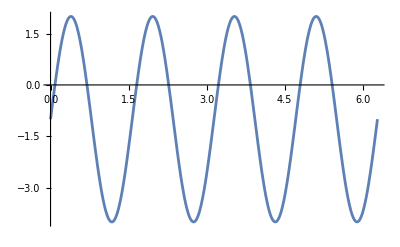

```mathematica
(* Static plot: *)
Plot[3 * Sin[4 * x] - 1, {x, 0, 2 * Pi}]
```

```mathematica
(* Dynamic plot: *)
Manipulate[
Plot[a * Sin[b * x + c], {x, 0, 2 * Pi}, ImagePadding -> 10] ,
{{a, 8, "Amplitude"}, 1, 10},
{{b, 2, "Frequency"}, 1, 10},
{{c, 1, "Phase"}, -10, 10}
]
```

While sliders are perhaps the most common control type, there are many others: buttons, checkboxes, popup menus, input fields….

More control types can be found in the following guide: Control Objects.

## Functional Programming

### Map

Map is a powerful function that maps a function to elements within an expression (typically a list):

```mathematica
Map[f,{a,b,c}]
```

{f[{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],f[{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}],f[c]}

Map lets you specify the level at which the function should be mapped (the default being level 1):

```mathematica
list={1,2,{a,b},3,4,{{c,d},{e,f}},5,6};
```

```mathematica
Map[f,list,3] (* Map down to level 3 *)
```

{f[1],f[2],f[{f[{f[0.658655],f[0.608878],f[0.902249],f[0.554452],f[0.0197205],f[0.683095],f[0.528947],f[0.309551],f[0.932973],f[0.184332],f[0.423354],f[0.476932],f[0.754761],f[0.372124],f[0.468918],f[0.955269],f[0.501441],f[0.105947],f[0.54768],f[0.412738],f[0.216176],f[0.51922],f[0.286272],f[0.113969],f[0.592962],f[0.821658],f[0.5624],f[0.623133],f[0.747305],f[0.810236],f[0.506901],f[0.395934],f[0.877304],f[0.580521],f[0.914746],f[0.380586],f[0.808145],f[0.991354],f[0.979217],f[0.79751],f[0.691302],f[0.0368366],f[0.212929],f[0.985529],f[0.360325],f[0.944286],f[0.968163],f[0.719601],f[0.965719],f[0.434916],f[0.0973516],f[0.886613],f[0.4808],f[0.865693],f[0.492682],f[0.0872864],f[0.55128],f[0.662186],f[0.717134],f[0.519963],f[0.918724],f[0.757666],f[0.893225],f[0.510302],f[0.561181],f[0.873508],f[0.740274],f[0.305044],f[0.458394],f[0.496888],f[0.76969],f[0.677791],f[0.199841],f[0.83469],f[0.607635],f[0.547533],f[0.408977],f[0.250906],f[0.0855991],f[0.652603],f[0.385517],f[0.135421],f[0.951168],f[0.140873],f[0.768399],f[0.0950527],f[0.944688],f[0.231095],f[0.0151312],f[0.545154],f[0.809348],f[0.371622],f[0.34478],f[0.93982],f[0.299787],f[0.0647148],f[0.723702],f[0.820204],f[0.410892],f[0.695915],f[0.429426],f[0.962443],f[0.452697],f[0.732557],f[0.140038],f[0.420644],f[0.0593377],f[0.119942],f[0.469197],f[0.425116],f[0.57572],f[0.737518],f[0.600768],f[0.0184617],f[0.124423],f[0.585911],f[0.0787141],f[0.147094],f[0.904256],f[0.825388],f[0.67528],f[0.284488],f[0.129479],f[0.846678],f[0.14352],f[0.847937],f[0.104034],f[0.450705],f[0.116324],f[0.977921],f[0.324633],f[0.832955],f[0.392104],f[0.960512],f[0.256188],f[0.0248205],f[0.170253],f[0.035447],f[0.64114],f[0.950047],f[0.200012],f[0.00171781],f[0.388779],f[0.126088],f[0.907316],f[0.338123],f[0.188098],f[0.720445],f[0.912486],f[0.373968],f[0.692498],f[0.100954],f[0.331277],f[0.966761],f[0.952563],f[0.383505],f[0.41017],f[0.340389],f[0.736583],f[0.15328],f[0.445827],f[0.329915],f[0.81347],f[0.513279],f[0.953631],f[0.437598],f[0.955787],f[0.127529],f[0.954351],f[0.173149],f[0.0257059],f[0.196325],f[0.513951],f[0.463924],f[0.426754],f[0.592117],f[0.236126],f[0.915636],f[0.0385059],f[0.841683],f[0.453929],f[0.0924965],f[0.806326],f[0.0280149],f[0.862022],f[0.786645],f[0.330564],f[0.171369],f[0.126639],f[0.434648],f[0.362864],f[0.390659],f[0.924989],f[0.299478],f[0.661203],f[0.630346],f[0.982481],f[0.135041],f[0.47187],f[0.322542],f[0.150995],f[0.602765],f[0.519226],f[0.857847],f[0.350704],f[0.282407],f[0.751888],f[0.209476],f[0.361908],f[0.1236],f[0.873031],f[0.0668491],f[0.729617],f[0.991063],f[0.740181],f[0.245957],f[0.892129],f[0.86385],f[0.677783],f[0.27735],f[0.042468],f[0.0221269],f[0.590829],f[0.139775],f[0.671614],f[0.373099],f[0.0544518],f[0.729354],f[0.0280032],f[0.298164],f[0.380569],f[0.060416],f[0.871374],f[0.398909],f[0.810089],f[0.0368148],f[0.571505],f[0.8752],f[0.820619],f[0.786736],f[0.465253],f[0.805004],f[0.950235],f[0.820954],f[0.30949],f[0.170407],f[0.32459],f[0.14378],f[0.813139],f[0.114947],f[0.261194],f[0.34254],f[0.499871],f[0.940269],f[0.854981],f[0.483211],f[0.384272],f[0.228039],f[0.043943],f[0.625523],f[0.354193],f[0.589057],f[0.0572985],f[0.267498],f[0.361911],f[0.926734],f[0.493792],f[0.476734],f[0.316166],f[0.684386],f[0.692453],f[0.37733],f[0.328863],f[0.870039],f[0.613768],f[0.548281],f[0.587107],f[0.110274],f[0.465296],f[0.764392],f[0.877914],f[0.333549],f[0.319611],f[0.48505],f[0.80242],f[0.40421],f[0.305568],f[0.944546],f[0.920135],f[0.645569],f[0.441436],f[0.342683],f[0.203527],f[0.247665],f[0.221012],f[0.636204],f[0.133609],f[0.368958],f[0.759727],f[0.363894],f[0.027277],f[0.0371021],f[0.770255],f[0.798415],f[0.761272],f[0.579626],f[0.473817],f[0.923827],f[0.00355128],f[0.680115],f[0.193197],f[0.643681],f[0.969257],f[0.508419],f[0.612342],f[0.812967],f[0.0803919],f[0.993571],f[0.883223],f[0.778037],f[0.867345],f[0.980072],f[0.496159],f[0.651497],f[0.130278],f[0.7797],f[0.128055],f[0.316308],f[0.369351],f[0.0969654],f[0.0428145],f[0.391802],f[0.812498],f[0.994246],f[0.803136],f[0.565049],f[0.226661],f[0.374876],f[0.256647],f[0.129228],f[0.708261],f[0.865834],f[0.674646],f[0.37647],f[0.197399],f[0.510162],f[0.0901534],f[0.139947],f[0.852319],f[0.981406],f[0.517378],f[0.167963],f[0.166701],f[0.296034],f[0.518259],f[0.0142394],f[0.636756],f[0.810141],f[0.889379],f[0.153446],f[0.797113],f[0.171016],f[0.15172],f[0.449199],f[0.470066],f[0.464406],f[0.200902],f[0.444615],f[0.19167],f[0.13435],f[0.225757],f[0.923396],f[0.524093],f[0.494041],f[0.895581],f[0.701225],f[0.842668],f[0.263119],f[0.298425],f[0.301901],f[0.958224],f[0.353295],f[0.647815],f[0.407721],f[0.962361],f[0.160866],f[0.0934846],f[0.758932],f[0.356149],f[0.409565],f[0.497057],f[0.434634],f[0.707251],f[0.164858],f[0.324204],f[0.38041],f[0.896131],f[0.46504],f[0.284969],f[0.28284],f[0.0947446],f[0.203081],f[0.150945],f[0.259577],f[0.828975],f[0.167203],f[0.0713126],f[0.249945],f[0.749587],f[0.965718],f[0.206411],f[0.0959492],f[0.67713],f[0.111517],f[0.333118],f[0.524548],f[0.456989],f[0.0281046],f[0.447315],f[0.203476],f[0.291081],f[0.365101],f[0.224602],f[0.893841],f[0.84979],f[0.958645],f[0.21283],f[0.217322],f[0.435983],f[0.155625],f[0.791132],f[0.967156],f[0.687024],f[0.127076],f[0.406924],f[0.316512],f[0.349657],f[0.340969],f[0.883887],f[0.927758],f[0.252834],f[0.942166],f[0.672152],f[0.782095],f[0.600791],f[0.197834],f[0.127009],f[0.221812],f[0.00210887],f[0.586926],f[0.983581],f[0.858366],f[0.848205],f[0.829971],f[0.983163],f[0.84479],f[0.405108],f[0.123636],f[0.535719],f[0.378957],f[0.681087],f[0.801735],f[0.109561],f[0.0617983],f[0.850685],f[0.840437],f[0.211927],f[0.607045],f[0.711326],f[0.203041],f[0.415603],f[0.295528],f[0.939539],f[0.890055],f[0.173413],f[0.459877],f[0.534153],f[0.192589],f[0.0327889],f[0.236054],f[0.545909],f[0.678176],f[0.406965],f[0.986602],f[0.493168],f[0.559006],f[0.973688],f[0.840122],f[0.651352],f[0.200643],f[0.829682],f[0.57113],f[0.142969],f[0.157981],f[0.396792],f[0.653167],f[0.146023],f[0.865579],f[0.164752],f[0.707725],f[0.622599],f[0.348621],f[0.345391],f[0.804633],f[0.911083],f[0.462758],f[0.96575],f[0.84451],f[0.703237],f[0.529091],f[0.295784],f[0.477567],f[0.304365],f[0.609282],f[0.758043],f[0.662622],f[0.910279],f[0.117909],f[0.261653],f[0.570719],f[0.684341],f[0.230884],f[0.903188],f[0.70509],f[0.437838],f[0.50547],f[0.0684499],f[0.946741],f[0.486141],f[0.81965],f[0.33112],f[0.599268],f[0.794865],f[0.33154],f[0.523739],f[0.696475],f[0.794025],f[0.2741],f[0.464242],f[0.142958],f[0.582567],f[0.626842],f[0.910964],f[0.194352],f[0.69566],f[0.521224],f[0.588375],f[0.223891],f[0.502475],f[0.526121],f[0.538817],f[0.602196],f[0.775143],f[0.696002],f[0.910379],f[0.235393],f[0.0905176],f[0.278262],f[0.959142],f[0.369805],f[0.82496],f[0.746942],f[0.107618],f[0.662012],f[0.31351],f[0.11094],f[0.577454],f[0.978901],f[0.295404],f[0.572866],f[0.405927],f[0.76002],f[0.189597],f[0.877502],f[0.922118],f[0.588165],f[0.778179],f[0.703634],f[0.954153],f[0.87253],f[0.149088],f[0.449983],f[0.481254],f[0.916914],f[0.928198],f[0.226245],f[0.838708],f[0.473027],f[0.62896],f[0.483024],f[0.747987],f[0.554526],f[0.194348],f[0.666514],f[0.427545],f[0.824823],f[0.501652],f[0.0162991],f[0.997239],f[0.0831793],f[0.603763],f[0.362054],f[0.253789],f[0.558793],f[0.180972],f[0.868262],f[0.381661],f[0.692478],f[0.143329],f[0.613135],f[0.166721],f[0.772223],f[0.631177],f[0.964033],f[0.610263],f[0.594802],f[0.772509],f[0.387348],f[0.767456],f[0.670647],f[0.665931],f[0.548578],f[0.687036],f[0.312399],f[0.724392],f[0.14524],f[0.150301],f[0.137198],f[0.178121],f[0.919114],f[0.566199],f[0.273703],f[0.744996],f[0.557592],f[0.249369],f[0.674379],f[0.62186],f[0.825551],f[0.0885031],f[0.696359],f[0.558231],f[0.748722],f[0.656938],f[0.735572],f[0.0316246],f[0.190047],f[0.371035],f[0.254022],f[0.858244],f[0.339954],f[0.933651],f[0.756104],f[0.153393],f[0.118459],f[0.525503],f[0.674453],f[0.5069],f[0.401608],f[0.655134],f[0.022673],f[0.83946],f[0.406734],f[0.848096],f[0.380155],f[0.0510664],f[0.929221],f[0.658821],f[0.130268],f[0.0599862],f[0.751039],f[0.888001],f[0.662228],f[0.83655],f[0.069542],f[0.0529975],f[0.406673],f[0.690784],f[0.668866],f[0.683935],f[0.293296],f[0.237907],f[0.233568],f[0.30582],f[0.761885],f[0.585756],f[0.127816],f[0.479001],f[0.351611],f[0.837024],f[0.877795],f[0.18781],f[0.596339],f[0.0947086],f[0.211603],f[0.881483],f[0.810353],f[0.937182],f[0.517695],f[0.682593],f[0.020296],f[0.060474],f[0.830867],f[0.424126],f[0.336553],f[0.156742],f[0.489192],f[0.820946],f[0.704764],f[0.72562],f[0.790548],f[0.811754],f[0.686453],f[0.267961],f[0.0707817],f[0.735738],f[0.205257],f[0.20159],f[0.530661],f[0.980191],f[0.961054],f[0.277042],f[0.627593],f[0.836571],f[0.0298689],f[0.927901],f[0.310047],f[0.606375],f[0.168765],f[0.0901116],f[0.587288],f[0.864652],f[0.221602],f[0.461208],f[0.742511],f[0.877007],f[0.460909],f[0.682491],f[0.153488],f[0.253426],f[0.0430687],f[0.399121],f[0.787822],f[0.810017],f[0.0297523],f[0.0322577],f[0.952671],f[0.0932073],f[0.690295],f[0.699609],f[0.962477],f[0.159062],f[0.255183],f[0.572179],f[0.36595],f[0.294387],f[0.428256],f[0.868104],f[0.57054],f[0.314278],f[0.335686],f[0.717118],f[0.835276],f[0.699522],f[0.931014],f[0.194588],f[0.574132],f[0.594307],f[0.231721],f[0.89581],f[0.901627],f[0.983179],f[0.752591],f[0.651953],f[0.452224],f[0.515572],f[0.356801],f[0.357162],f[0.766998],f[0.892473],f[0.158167],f[0.577625],f[0.503967],f[0.271357],f[0.561339],f[0.353881],f[0.0133146],f[0.110947],f[0.623532],f[0.680314],f[0.051564],f[0.769999],f[0.214855],f[0.356454],f[0.939785],f[0.450581],f[0.307273],f[0.143898],f[0.110823],f[0.600707],f[0.825946],f[0.729725],f[0.161873],f[0.772659],f[0.42477],f[0.195428],f[0.303112],f[0.192551],f[0.979186],f[0.716386],f[0.860548],f[0.117022],f[0.522469],f[0.411321],f[0.929085],f[0.951884],f[0.232108],f[0.944376],f[0.792816],f[0.676077],f[0.163303],f[0.787668],f[0.640759],f[0.759886],f[0.511421],f[0.453798],f[0.126802],f[0.135509],f[0.812841],f[0.955347],f[0.364687],f[0.470782],f[0.49958],f[0.814559],f[0.969725],f[0.305732],f[0.539777],f[0.993454],f[0.299862],f[0.0951853],f[0.964347],f[0.37939],f[0.368771],f[0.061539],f[0.0749235],f[0.111674],f[0.560951],f[0.468625],f[0.0076525],f[0.93525],f[0.992087],f[0.892142],f[0.678951],f[0.898595],f[0.0122218],f[0.528737],f[0.379741],f[0.941471],f[0.204908],f[0.122855],f[0.26245],f[0.918234],f[0.0922731],f[0.691934],f[0.250592],f[0.112558],f[0.799727],f[0.668539],f[0.0371164],f[0.92641],f[0.836081],f[0.36804],f[0.260871],f[0.438383],f[0.226896],f[0.545265],f[0.752025],f[0.760565],f[0.885855],f[0.904922],f[0.61499],f[0.640233],f[0.297068],f[0.605774],f[0.0623011],f[0.422942],f[0.0643373],f[0.33587],f[0.722033],f[0.523307],f[0.813771],f[0.398731],f[0.126644],f[0.302599],f[0.962368],f[0.628099],f[0.261086],f[0.355512],f[0.805515],f[0.797799],f[0.960518],f[0.0860143],f[0.59743],f[0.826742],f[0.108156],f[0.444083],f[0.794857],f[0.321074],f[0.276959],f[0.28833],f[0.840363],f[0.507724],f[0.415414],f[0.454891],f[0.0325609],f[0.329123],f[0.404387],f[0.758319],f[0.587038],f[0.773281],f[0.556504],f[0.322849],f[0.584639],f[0.83844],f[0.594459],f[0.838405],f[0.146914],f[0.997219],f[0.358361],f[0.723518],f[0.946605],f[0.210501],f[0.821239],f[0.0955331],f[0.772493],f[0.607056],f[0.141751],f[0.384634],f[0.0978196],f[0.143842],f[0.457943],f[0.587907],f[0.310708],f[0.846183],f[0.277551],f[0.535662],f[0.607733],f[0.693516],f[0.532404],f[0.126237],f[0.842159],f[0.576824],f[0.9455],f[0.0583295],f[0.727337],f[0.583855],f[0.434433],f[0.40197],f[0.629844],f[0.314241],f[0.0859739],f[0.438185],f[0.436257],f[0.394376],f[0.0158427],f[0.787632],f[0.596952],f[0.979742],f[0.0353883],f[0.524162],f[0.13702],f[0.86815],f[0.818112],f[0.739273],f[0.395685],f[0.0269059],f[0.664728],f[0.39939],f[0.355841],f[0.514433],f[0.02094],f[0.210257],f[0.126071],f[0.216787],f[0.312661],f[0.380271],f[0.183956],f[0.498664],f[0.828604],f[0.319766],f[0.338799],f[0.0943974],f[0.01056],f[0.673983],f[0.00785435],f[0.0636842],f[0.0366003],f[0.0717747],f[0.931251],f[0.31199],f[0.607297]}],f[{f[0.664609],f[0.761459],f[0.932727],f[0.170838],f[0.324969],f[0.439794],f[0.921],f[0.303474],f[0.294229],f[0.214684],f[0.48881],f[0.928019],f[0.4927],f[0.409977],f[0.770972],f[0.880431],f[0.206347],f[0.0774461],f[0.568148],f[0.456393],f[0.610448],f[0.863655],f[0.0113171],f[0.362465],f[0.835952],f[0.135436],f[0.747527],f[0.522848],f[0.256557],f[0.18966],f[0.218257],f[0.250761],f[0.615859],f[0.259958],f[0.514642],f[0.654624],f[0.236517],f[0.790386],f[0.378998],f[0.320828],f[0.785302],f[0.827512],f[0.247222],f[0.646603],f[0.678712],f[0.353927],f[0.80647],f[0.136581],f[0.906641],f[0.773834],f[0.025797],f[0.426371],f[0.0691717],f[0.262658],f[0.479239],f[0.686493],f[0.36393],f[0.933343],f[0.0225602],f[0.567217],f[0.611998],f[0.331482],f[0.825952],f[0.727796],f[0.700949],f[0.230738],f[0.0595383],f[0.513299],f[0.564256],f[0.229428],f[0.78721],f[0.691514],f[0.165997],f[0.34006],f[0.788176],f[0.670254],f[0.351728],f[0.626052],f[0.112668],f[0.538503],f[0.57938],f[0.571805],f[0.686771],f[0.339316],f[0.796498],f[0.614084],f[0.737121],f[0.0942116],f[0.80599],f[0.291841],f[0.0130051],f[0.395759],f[0.988115],f[0.0542776],f[0.22346],f[0.926411],f[0.0903764],f[0.0200568],f[0.886513],f[0.580481],f[0.584832],f[0.257576],f[0.358462],f[0.841214],f[0.804814],f[0.580295],f[0.964294],f[0.0610372],f[0.500554],f[0.30907],f[0.710943],f[0.405803],f[0.111084],f[0.207939],f[0.856794],f[0.976047],f[0.130686],f[0.163152],f[0.921303],f[0.476744],f[0.436688],f[0.806607],f[0.863352],f[0.571144],f[0.945527],f[0.145048],f[0.814619],f[0.0548375],f[0.794493],f[0.0127239],f[0.0675948],f[0.283145],f[0.090085],f[0.470912],f[0.921384],f[0.920124],f[0.526853],f[0.175496],f[0.674855],f[0.655907],f[0.327103],f[0.207757],f[0.956869],f[0.0964553],f[0.916109],f[0.526289],f[0.0813583],f[0.748876],f[0.703413],f[0.559478],f[0.60333],f[0.658778],f[0.92798],f[0.0197046],f[0.232221],f[0.812925],f[0.17365],f[0.560214],f[0.636285],f[0.195297],f[0.789061],f[0.67307],f[0.437337],f[0.282184],f[0.0481526],f[0.445093],f[0.609226],f[0.174011],f[0.609111],f[0.0842214],f[0.0295397],f[0.357952],f[0.807712],f[0.974775],f[0.587482],f[0.0334009],f[0.503003],f[0.255578],f[0.911882],f[0.174357],f[0.56814],f[0.542007],f[0.963626],f[0.103944],f[0.205846],f[0.998914],f[0.915078],f[0.725774],f[0.457071],f[0.14304],f[0.942747],f[0.823999],f[0.373148],f[0.0934681],f[0.598288],f[0.131829],f[0.407614],f[0.969254],f[0.402363],f[0.496296],f[0.243362],f[0.0350186],f[0.0338795],f[0.408042],f[0.395984],f[0.709139],f[0.192731],f[0.6238],f[0.945207],f[0.0867849],f[0.32137],f[0.597948],f[0.950451],f[0.257986],f[0.446386],f[0.883147],f[0.811697],f[0.890873],f[0.897184],f[0.891753],f[0.575128],f[0.0505107],f[0.569497],f[0.708516],f[0.945408],f[0.391715],f[0.403614],f[0.44765],f[0.424776],f[0.732546],f[0.246708],f[0.857798],f[0.382583],f[0.458746],f[0.797527],f[0.457687],f[0.138466],f[0.16867],f[0.61954],f[0.341234],f[0.648792],f[0.983168],f[0.635297],f[0.973276],f[0.792998],f[0.616919],f[0.699181],f[0.914147],f[0.716952],f[0.65611],f[0.0795228],f[0.380921],f[0.620416],f[0.558515],f[0.413285],f[0.935023],f[0.159023],f[0.894121],f[0.140695],f[0.0307446],f[0.262641],f[0.349305],f[0.772422],f[0.388953],f[0.244447],f[0.211688],f[0.246017],f[0.848555],f[0.969056],f[0.556571],f[0.53947],f[0.952684],f[0.120085],f[0.820911],f[0.944346],f[0.136659],f[0.610533],f[0.118838],f[0.401901],f[0.208345],f[0.0167604],f[0.368023],f[0.467991],f[0.163649],f[0.259239],f[0.0568464],f[0.16984],f[0.833806],f[0.0288012],f[0.907995],f[0.51241],f[0.135644],f[0.59304],f[0.0406054],f[0.524838],f[0.615425],f[0.888944],f[0.00893688],f[0.666359],f[0.105276],f[0.831572],f[0.538661],f[0.521234],f[0.19952],f[0.29194],f[0.189421],f[0.657562],f[0.259267],f[0.609808],f[0.0472932],f[0.738547],f[0.366133],f[0.707757],f[0.393087],f[0.0415082],f[0.311202],f[0.674714],f[0.904324],f[0.773655],f[0.735368],f[0.935112],f[0.529052],f[0.974022],f[0.304483],f[0.382105],f[0.222994],f[0.607676],f[0.597753],f[0.105499],f[0.842858],f[0.234941],f[0.709189],f[0.873981],f[0.937954],f[0.445753],f[0.344964],f[0.266259],f[0.0299797],f[0.984419],f[0.996667],f[0.682],f[0.184653],f[0.413385],f[0.381635],f[0.266133],f[0.132417],f[0.267231],f[0.829543],f[0.771882],f[0.680847],f[0.770278],f[0.517215],f[0.721376],f[0.78358],f[0.572401],f[0.411786],f[0.188749],f[0.0798975],f[0.983359],f[0.142521],f[0.562941],f[0.539257],f[0.331913],f[0.409437],f[0.977139],f[0.0537387],f[0.881859],f[0.391277],f[0.96878],f[0.624528],f[0.320429],f[0.704753],f[0.498484],f[0.445255],f[0.185914],f[0.235829],f[0.667213],f[0.940603],f[0.777617],f[0.064541],f[0.905907],f[0.297621],f[0.615675],f[0.626472],f[0.454853],f[0.207772],f[0.546067],f[0.578265],f[0.701642],f[0.144575],f[0.22643],f[0.716251],f[0.903809],f[0.979112],f[0.771597],f[0.398435],f[0.170287],f[0.406241],f[0.69234],f[0.898633],f[0.205524],f[0.126373],f[0.667353],f[0.560987],f[0.0776578],f[0.487791],f[0.0776204],f[0.640148],f[0.127693],f[0.201068],f[0.0343942],f[0.277051],f[0.762392],f[0.696579],f[0.915393],f[0.651206],f[0.348316],f[0.119192],f[0.954117],f[0.800435],f[0.863157],f[0.521069],f[0.287147],f[0.98349],f[0.898606],f[0.0490855],f[0.920608],f[0.531592],f[0.77106],f[0.55058],f[0.761712],f[0.883465],f[0.041762],f[0.735827],f[0.663417],f[0.255177],f[0.611874],f[0.704554],f[0.631175],f[0.433336],f[0.35155],f[0.249081],f[0.611914],f[0.319632],f[0.492302],f[0.711595],f[0.211789],f[0.8925],f[0.687978],f[0.151161],f[0.889642],f[0.138627],f[0.97967],f[0.212456],f[0.907777],f[0.791521],f[0.886086],f[0.805803],f[0.597498],f[0.211648],f[0.221435],f[0.787649],f[0.111074],f[0.555712],f[0.943343],f[0.287086],f[0.126684],f[0.00877993],f[0.774669],f[0.843703],f[0.194847],f[0.796989],f[0.494541],f[0.629946],f[0.0544362],f[0.875606],f[0.0561401],f[0.883061],f[0.760036],f[0.836996],f[0.42751],f[0.822598],f[0.0179507],f[0.100862],f[0.217081],f[0.123015],f[0.348285],f[0.812974],f[0.532222],f[0.321022],f[0.256694],f[0.0927401],f[0.169377],f[0.466168],f[0.925026],f[0.939327],f[0.779273],f[0.765064],f[0.960103],f[0.314062],f[0.870813],f[0.995323],f[0.0436449],f[0.354766],f[0.00351348],f[0.36764],f[0.69052],f[0.485661],f[0.0503631],f[0.461638],f[0.189361],f[0.239859],f[0.356121],f[0.0165457],f[0.743029],f[0.0511236],f[0.528454],f[0.938471],f[0.121942],f[0.921587],f[0.183532],f[0.892992],f[0.308484],f[0.269307],f[0.729423],f[0.163781],f[0.661396],f[0.358302],f[0.621855],f[0.839771],f[0.477455],f[0.964795],f[0.431092],f[0.418989],f[0.482102],f[0.646781],f[0.312924],f[0.102695],f[0.646531],f[0.276958],f[0.251136],f[0.689144],f[0.334886],f[0.692469],f[0.456294],f[0.942485],f[0.710828],f[0.933556],f[0.531676],f[0.0617303],f[0.170642],f[0.419584],f[0.518832],f[0.99964],f[0.425148],f[0.879695],f[0.0619825],f[0.582331],f[0.89319],f[0.152669],f[0.895011],f[0.698235],f[0.205927],f[0.254221],f[0.247554],f[0.988221],f[0.0802619],f[0.354812],f[0.334618],f[0.0410436],f[0.101042],f[0.805072],f[0.421357],f[0.162031],f[0.600318],f[0.918943],f[0.727133],f[0.291282],f[0.990232],f[0.196143],f[0.29158],f[0.435355],f[0.998098],f[0.470137],f[0.0945442],f[0.676703],f[0.436028],f[0.184384],f[0.0135357],f[0.838483],f[0.817216],f[0.234716],f[0.842311],f[0.698066],f[0.249039],f[0.235242],f[0.674137],f[0.882525],f[0.699814],f[0.817708],f[0.609034],f[0.919796],f[0.500953],f[0.0211187],f[0.570723],f[0.811272],f[0.472408],f[0.195122],f[0.856461],f[0.00351917],f[0.894163],f[0.442515],f[0.532447],f[0.648212],f[0.918433],f[0.193021],f[0.326604],f[0.715285],f[0.728211],f[0.00718574],f[0.431291],f[0.767957],f[0.96388],f[0.11974],f[0.422136],f[0.626472],f[0.131115],f[0.654874],f[0.13075],f[0.355507],f[0.521186],f[0.443028],f[0.968815],f[0.217521],f[0.725638],f[0.196835],f[0.720685],f[0.805805],f[0.623683],f[0.911844],f[0.265088],f[0.856165],f[0.779509],f[0.69749],f[0.786313],f[0.755328],f[0.706338],f[0.0512227],f[0.830798],f[0.923198],f[0.603011],f[0.861201],f[0.895699],f[0.250385],f[0.41356],f[0.686995],f[0.397118],f[0.233285],f[0.573668],f[0.223501],f[0.920575],f[0.867161],f[0.843205],f[0.525829],f[0.401813],f[0.930629],f[0.160176],f[0.934402],f[0.337303],f[0.599207],f[0.568588],f[0.217133],f[0.333475],f[0.23174],f[0.941062],f[0.0258093],f[0.916391],f[0.483808],f[0.442209],f[0.690075],f[0.521745],f[0.715078],f[0.818351],f[0.0690708],f[0.16204],f[0.730011],f[0.263587],f[0.38724],f[0.720871],f[0.317657],f[0.0110402],f[0.40648],f[0.344691],f[0.468733],f[0.118313],f[0.566701],f[0.468755],f[0.175745],f[0.189884],f[0.540356],f[0.375667],f[0.629106],f[0.144508],f[0.386069],f[0.6139],f[0.853258],f[0.742531],f[0.203219],f[0.410004],f[0.771592],f[0.587019],f[0.790705],f[0.0379853],f[0.0705683],f[0.375218],f[0.521129],f[0.834368],f[0.772281],f[0.25326],f[0.0608575],f[0.838213],f[0.0828329],f[0.415786],f[0.789892],f[0.0772127],f[0.248565],f[0.641989],f[0.539598],f[0.666127],f[0.0341072],f[0.326549],f[0.273681],f[0.863591],f[0.540367],f[0.419135],f[0.435139],f[0.322812],f[0.272004],f[0.613232],f[0.870786],f[0.730702],f[0.973229],f[0.139658],f[0.217151],f[0.190403],f[0.280563],f[0.427835],f[0.98927],f[0.205727],f[0.368518],f[0.727837],f[0.682958],f[0.560968],f[0.305405],f[0.748968],f[0.966703],f[0.246063],f[0.491496],f[0.353261],f[0.187702],f[0.825254],f[0.50366],f[0.774974],f[0.618229],f[0.75377],f[0.922113],f[0.855709],f[0.35905],f[0.27117],f[0.153095],f[0.433065],f[0.578757],f[0.245847],f[0.0893512],f[0.519061],f[0.102663],f[0.328187],f[0.747206],f[0.0488964],f[0.558168],f[0.198365],f[0.0688112],f[0.463616],f[0.129045],f[0.795083],f[0.217812],f[0.21686],f[0.0431795],f[0.627674],f[0.323578],f[0.909234],f[0.446375],f[0.278607],f[0.0957293],f[0.220422],f[0.347752],f[0.693609],f[0.876373],f[0.640024],f[0.447684],f[0.81062],f[0.723226],f[0.694546],f[0.319464],f[0.451046],f[0.396871],f[0.614496],f[0.7876],f[0.483851],f[0.284356],f[0.456648],f[0.783586],f[0.676054],f[0.354319],f[0.0997906],f[0.908647],f[0.92983],f[0.0272409],f[0.00595076],f[0.971716],f[0.354938],f[0.612259],f[0.0793553],f[0.365908],f[0.298232],f[0.0309158],f[0.818084],f[0.688351],f[0.205641],f[0.276862],f[0.609032],f[0.776876],f[0.367277],f[0.657691],f[0.505318],f[0.159789],f[0.716392],f[0.598718],f[0.233447],f[0.0861608],f[0.95797],f[0.940375],f[0.964809],f[0.732921],f[0.15859],f[0.0426767],f[0.00908598],f[0.274411],f[0.933174],f[0.686216],f[0.487726],f[0.636754],f[0.812809],f[0.338219],f[0.779084],f[0.202766],f[0.654673],f[0.492388],f[0.121695],f[0.409542],f[0.0924109],f[0.459057],f[0.398511],f[0.728781],f[0.891843],f[0.287376],f[0.57183],f[0.593072],f[0.118004],f[0.0580708],f[0.259754],f[0.742112],f[0.181491],f[0.0390932],f[0.879712],f[0.371308],f[0.256144],f[0.616864],f[0.329561],f[0.274741],f[0.71832],f[0.2406],f[0.863532],f[0.451076],f[0.764703],f[0.16387],f[0.440733],f[0.266797],f[0.147085],f[0.521666],f[0.973431],f[0.653259],f[0.139564],f[0.568973],f[0.189693],f[0.988945],f[0.768582],f[0.32313],f[0.59834],f[0.268145],f[0.977263],f[0.577533],f[0.319657],f[0.17484],f[0.75356],f[0.0814859],f[0.729307],f[0.277091],f[0.461169],f[0.0734133],f[0.111328],f[0.56394],f[0.282433],f[0.0223517],f[0.448281],f[0.63011],f[0.111092],f[0.857437],f[0.783147],f[0.0686123],f[0.804222],f[0.868872],f[0.615046],f[0.182784],f[0.255308],f[0.0801911],f[0.168925],f[0.580517],f[0.692816],f[0.259943],f[0.272213],f[0.254848],f[0.367135],f[0.413386],f[0.206532],f[0.141322],f[0.800835],f[0.63847],f[0.559113],f[0.650895],f[0.459881],f[0.0860842],f[0.440644],f[0.709609],f[0.757485],f[0.864458],f[0.826222],f[0.144459],f[0.27012],f[0.485539],f[0.555773],f[0.202999],f[0.959652],f[0.443637],f[0.877259],f[0.76047],f[0.218818],f[0.453241],f[0.877678],f[0.0628503],f[0.0249376],f[0.0674061],f[0.66154],f[0.705562],f[0.178923],f[0.304747],f[0.727845],f[0.948617],f[0.726193],f[0.622498],f[0.196008],f[0.946614],f[0.826382],f[0.560411],f[0.791164],f[0.982341],f[0.780333],f[0.0233497],f[0.684833],f[0.491442],f[0.844375],f[0.206253],f[0.911558],f[0.680892],f[0.575932],f[0.203484],f[0.885864],f[0.259445],f[0.289792],f[0.442195],f[0.0435101],f[0.843666],f[0.588271],f[0.885709],f[0.339127],f[0.098198],f[0.822982],f[0.0470089],f[0.751378],f[0.492828]}]}],f[3],f[4],f[{f[{f[c],f[d]}],f[{f[e],f[f]}]}],f[5],f[6]}

```mathematica
Map[f,list,{3}] (* Map at level 3 only *)
```

{1,2,{{f[0.658655],f[0.608878],f[0.902249],f[0.554452],f[0.0197205],f[0.683095],f[0.528947],f[0.309551],f[0.932973],f[0.184332],f[0.423354],f[0.476932],f[0.754761],f[0.372124],f[0.468918],f[0.955269],f[0.501441],f[0.105947],f[0.54768],f[0.412738],f[0.216176],f[0.51922],f[0.286272],f[0.113969],f[0.592962],f[0.821658],f[0.5624],f[0.623133],f[0.747305],f[0.810236],f[0.506901],f[0.395934],f[0.877304],f[0.580521],f[0.914746],f[0.380586],f[0.808145],f[0.991354],f[0.979217],f[0.79751],f[0.691302],f[0.0368366],f[0.212929],f[0.985529],f[0.360325],f[0.944286],f[0.968163],f[0.719601],f[0.965719],f[0.434916],f[0.0973516],f[0.886613],f[0.4808],f[0.865693],f[0.492682],f[0.0872864],f[0.55128],f[0.662186],f[0.717134],f[0.519963],f[0.918724],f[0.757666],f[0.893225],f[0.510302],f[0.561181],f[0.873508],f[0.740274],f[0.305044],f[0.458394],f[0.496888],f[0.76969],f[0.677791],f[0.199841],f[0.83469],f[0.607635],f[0.547533],f[0.408977],f[0.250906],f[0.0855991],f[0.652603],f[0.385517],f[0.135421],f[0.951168],f[0.140873],f[0.768399],f[0.0950527],f[0.944688],f[0.231095],f[0.0151312],f[0.545154],f[0.809348],f[0.371622],f[0.34478],f[0.93982],f[0.299787],f[0.0647148],f[0.723702],f[0.820204],f[0.410892],f[0.695915],f[0.429426],f[0.962443],f[0.452697],f[0.732557],f[0.140038],f[0.420644],f[0.0593377],f[0.119942],f[0.469197],f[0.425116],f[0.57572],f[0.737518],f[0.600768],f[0.0184617],f[0.124423],f[0.585911],f[0.0787141],f[0.147094],f[0.904256],f[0.825388],f[0.67528],f[0.284488],f[0.129479],f[0.846678],f[0.14352],f[0.847937],f[0.104034],f[0.450705],f[0.116324],f[0.977921],f[0.324633],f[0.832955],f[0.392104],f[0.960512],f[0.256188],f[0.0248205],f[0.170253],f[0.035447],f[0.64114],f[0.950047],f[0.200012],f[0.00171781],f[0.388779],f[0.126088],f[0.907316],f[0.338123],f[0.188098],f[0.720445],f[0.912486],f[0.373968],f[0.692498],f[0.100954],f[0.331277],f[0.966761],f[0.952563],f[0.383505],f[0.41017],f[0.340389],f[0.736583],f[0.15328],f[0.445827],f[0.329915],f[0.81347],f[0.513279],f[0.953631],f[0.437598],f[0.955787],f[0.127529],f[0.954351],f[0.173149],f[0.0257059],f[0.196325],f[0.513951],f[0.463924],f[0.426754],f[0.592117],f[0.236126],f[0.915636],f[0.0385059],f[0.841683],f[0.453929],f[0.0924965],f[0.806326],f[0.0280149],f[0.862022],f[0.786645],f[0.330564],f[0.171369],f[0.126639],f[0.434648],f[0.362864],f[0.390659],f[0.924989],f[0.299478],f[0.661203],f[0.630346],f[0.982481],f[0.135041],f[0.47187],f[0.322542],f[0.150995],f[0.602765],f[0.519226],f[0.857847],f[0.350704],f[0.282407],f[0.751888],f[0.209476],f[0.361908],f[0.1236],f[0.873031],f[0.0668491],f[0.729617],f[0.991063],f[0.740181],f[0.245957],f[0.892129],f[0.86385],f[0.677783],f[0.27735],f[0.042468],f[0.0221269],f[0.590829],f[0.139775],f[0.671614],f[0.373099],f[0.0544518],f[0.729354],f[0.0280032],f[0.298164],f[0.380569],f[0.060416],f[0.871374],f[0.398909],f[0.810089],f[0.0368148],f[0.571505],f[0.8752],f[0.820619],f[0.786736],f[0.465253],f[0.805004],f[0.950235],f[0.820954],f[0.30949],f[0.170407],f[0.32459],f[0.14378],f[0.813139],f[0.114947],f[0.261194],f[0.34254],f[0.499871],f[0.940269],f[0.854981],f[0.483211],f[0.384272],f[0.228039],f[0.043943],f[0.625523],f[0.354193],f[0.589057],f[0.0572985],f[0.267498],f[0.361911],f[0.926734],f[0.493792],f[0.476734],f[0.316166],f[0.684386],f[0.692453],f[0.37733],f[0.328863],f[0.870039],f[0.613768],f[0.548281],f[0.587107],f[0.110274],f[0.465296],f[0.764392],f[0.877914],f[0.333549],f[0.319611],f[0.48505],f[0.80242],f[0.40421],f[0.305568],f[0.944546],f[0.920135],f[0.645569],f[0.441436],f[0.342683],f[0.203527],f[0.247665],f[0.221012],f[0.636204],f[0.133609],f[0.368958],f[0.759727],f[0.363894],f[0.027277],f[0.0371021],f[0.770255],f[0.798415],f[0.761272],f[0.579626],f[0.473817],f[0.923827],f[0.00355128],f[0.680115],f[0.193197],f[0.643681],f[0.969257],f[0.508419],f[0.612342],f[0.812967],f[0.0803919],f[0.993571],f[0.883223],f[0.778037],f[0.867345],f[0.980072],f[0.496159],f[0.651497],f[0.130278],f[0.7797],f[0.128055],f[0.316308],f[0.369351],f[0.0969654],f[0.0428145],f[0.391802],f[0.812498],f[0.994246],f[0.803136],f[0.565049],f[0.226661],f[0.374876],f[0.256647],f[0.129228],f[0.708261],f[0.865834],f[0.674646],f[0.37647],f[0.197399],f[0.510162],f[0.0901534],f[0.139947],f[0.852319],f[0.981406],f[0.517378],f[0.167963],f[0.166701],f[0.296034],f[0.518259],f[0.0142394],f[0.636756],f[0.810141],f[0.889379],f[0.153446],f[0.797113],f[0.171016],f[0.15172],f[0.449199],f[0.470066],f[0.464406],f[0.200902],f[0.444615],f[0.19167],f[0.13435],f[0.225757],f[0.923396],f[0.524093],f[0.494041],f[0.895581],f[0.701225],f[0.842668],f[0.263119],f[0.298425],f[0.301901],f[0.958224],f[0.353295],f[0.647815],f[0.407721],f[0.962361],f[0.160866],f[0.0934846],f[0.758932],f[0.356149],f[0.409565],f[0.497057],f[0.434634],f[0.707251],f[0.164858],f[0.324204],f[0.38041],f[0.896131],f[0.46504],f[0.284969],f[0.28284],f[0.0947446],f[0.203081],f[0.150945],f[0.259577],f[0.828975],f[0.167203],f[0.0713126],f[0.249945],f[0.749587],f[0.965718],f[0.206411],f[0.0959492],f[0.67713],f[0.111517],f[0.333118],f[0.524548],f[0.456989],f[0.0281046],f[0.447315],f[0.203476],f[0.291081],f[0.365101],f[0.224602],f[0.893841],f[0.84979],f[0.958645],f[0.21283],f[0.217322],f[0.435983],f[0.155625],f[0.791132],f[0.967156],f[0.687024],f[0.127076],f[0.406924],f[0.316512],f[0.349657],f[0.340969],f[0.883887],f[0.927758],f[0.252834],f[0.942166],f[0.672152],f[0.782095],f[0.600791],f[0.197834],f[0.127009],f[0.221812],f[0.00210887],f[0.586926],f[0.983581],f[0.858366],f[0.848205],f[0.829971],f[0.983163],f[0.84479],f[0.405108],f[0.123636],f[0.535719],f[0.378957],f[0.681087],f[0.801735],f[0.109561],f[0.0617983],f[0.850685],f[0.840437],f[0.211927],f[0.607045],f[0.711326],f[0.203041],f[0.415603],f[0.295528],f[0.939539],f[0.890055],f[0.173413],f[0.459877],f[0.534153],f[0.192589],f[0.0327889],f[0.236054],f[0.545909],f[0.678176],f[0.406965],f[0.986602],f[0.493168],f[0.559006],f[0.973688],f[0.840122],f[0.651352],f[0.200643],f[0.829682],f[0.57113],f[0.142969],f[0.157981],f[0.396792],f[0.653167],f[0.146023],f[0.865579],f[0.164752],f[0.707725],f[0.622599],f[0.348621],f[0.345391],f[0.804633],f[0.911083],f[0.462758],f[0.96575],f[0.84451],f[0.703237],f[0.529091],f[0.295784],f[0.477567],f[0.304365],f[0.609282],f[0.758043],f[0.662622],f[0.910279],f[0.117909],f[0.261653],f[0.570719],f[0.684341],f[0.230884],f[0.903188],f[0.70509],f[0.437838],f[0.50547],f[0.0684499],f[0.946741],f[0.486141],f[0.81965],f[0.33112],f[0.599268],f[0.794865],f[0.33154],f[0.523739],f[0.696475],f[0.794025],f[0.2741],f[0.464242],f[0.142958],f[0.582567],f[0.626842],f[0.910964],f[0.194352],f[0.69566],f[0.521224],f[0.588375],f[0.223891],f[0.502475],f[0.526121],f[0.538817],f[0.602196],f[0.775143],f[0.696002],f[0.910379],f[0.235393],f[0.0905176],f[0.278262],f[0.959142],f[0.369805],f[0.82496],f[0.746942],f[0.107618],f[0.662012],f[0.31351],f[0.11094],f[0.577454],f[0.978901],f[0.295404],f[0.572866],f[0.405927],f[0.76002],f[0.189597],f[0.877502],f[0.922118],f[0.588165],f[0.778179],f[0.703634],f[0.954153],f[0.87253],f[0.149088],f[0.449983],f[0.481254],f[0.916914],f[0.928198],f[0.226245],f[0.838708],f[0.473027],f[0.62896],f[0.483024],f[0.747987],f[0.554526],f[0.194348],f[0.666514],f[0.427545],f[0.824823],f[0.501652],f[0.0162991],f[0.997239],f[0.0831793],f[0.603763],f[0.362054],f[0.253789],f[0.558793],f[0.180972],f[0.868262],f[0.381661],f[0.692478],f[0.143329],f[0.613135],f[0.166721],f[0.772223],f[0.631177],f[0.964033],f[0.610263],f[0.594802],f[0.772509],f[0.387348],f[0.767456],f[0.670647],f[0.665931],f[0.548578],f[0.687036],f[0.312399],f[0.724392],f[0.14524],f[0.150301],f[0.137198],f[0.178121],f[0.919114],f[0.566199],f[0.273703],f[0.744996],f[0.557592],f[0.249369],f[0.674379],f[0.62186],f[0.825551],f[0.0885031],f[0.696359],f[0.558231],f[0.748722],f[0.656938],f[0.735572],f[0.0316246],f[0.190047],f[0.371035],f[0.254022],f[0.858244],f[0.339954],f[0.933651],f[0.756104],f[0.153393],f[0.118459],f[0.525503],f[0.674453],f[0.5069],f[0.401608],f[0.655134],f[0.022673],f[0.83946],f[0.406734],f[0.848096],f[0.380155],f[0.0510664],f[0.929221],f[0.658821],f[0.130268],f[0.0599862],f[0.751039],f[0.888001],f[0.662228],f[0.83655],f[0.069542],f[0.0529975],f[0.406673],f[0.690784],f[0.668866],f[0.683935],f[0.293296],f[0.237907],f[0.233568],f[0.30582],f[0.761885],f[0.585756],f[0.127816],f[0.479001],f[0.351611],f[0.837024],f[0.877795],f[0.18781],f[0.596339],f[0.0947086],f[0.211603],f[0.881483],f[0.810353],f[0.937182],f[0.517695],f[0.682593],f[0.020296],f[0.060474],f[0.830867],f[0.424126],f[0.336553],f[0.156742],f[0.489192],f[0.820946],f[0.704764],f[0.72562],f[0.790548],f[0.811754],f[0.686453],f[0.267961],f[0.0707817],f[0.735738],f[0.205257],f[0.20159],f[0.530661],f[0.980191],f[0.961054],f[0.277042],f[0.627593],f[0.836571],f[0.0298689],f[0.927901],f[0.310047],f[0.606375],f[0.168765],f[0.0901116],f[0.587288],f[0.864652],f[0.221602],f[0.461208],f[0.742511],f[0.877007],f[0.460909],f[0.682491],f[0.153488],f[0.253426],f[0.0430687],f[0.399121],f[0.787822],f[0.810017],f[0.0297523],f[0.0322577],f[0.952671],f[0.0932073],f[0.690295],f[0.699609],f[0.962477],f[0.159062],f[0.255183],f[0.572179],f[0.36595],f[0.294387],f[0.428256],f[0.868104],f[0.57054],f[0.314278],f[0.335686],f[0.717118],f[0.835276],f[0.699522],f[0.931014],f[0.194588],f[0.574132],f[0.594307],f[0.231721],f[0.89581],f[0.901627],f[0.983179],f[0.752591],f[0.651953],f[0.452224],f[0.515572],f[0.356801],f[0.357162],f[0.766998],f[0.892473],f[0.158167],f[0.577625],f[0.503967],f[0.271357],f[0.561339],f[0.353881],f[0.0133146],f[0.110947],f[0.623532],f[0.680314],f[0.051564],f[0.769999],f[0.214855],f[0.356454],f[0.939785],f[0.450581],f[0.307273],f[0.143898],f[0.110823],f[0.600707],f[0.825946],f[0.729725],f[0.161873],f[0.772659],f[0.42477],f[0.195428],f[0.303112],f[0.192551],f[0.979186],f[0.716386],f[0.860548],f[0.117022],f[0.522469],f[0.411321],f[0.929085],f[0.951884],f[0.232108],f[0.944376],f[0.792816],f[0.676077],f[0.163303],f[0.787668],f[0.640759],f[0.759886],f[0.511421],f[0.453798],f[0.126802],f[0.135509],f[0.812841],f[0.955347],f[0.364687],f[0.470782],f[0.49958],f[0.814559],f[0.969725],f[0.305732],f[0.539777],f[0.993454],f[0.299862],f[0.0951853],f[0.964347],f[0.37939],f[0.368771],f[0.061539],f[0.0749235],f[0.111674],f[0.560951],f[0.468625],f[0.0076525],f[0.93525],f[0.992087],f[0.892142],f[0.678951],f[0.898595],f[0.0122218],f[0.528737],f[0.379741],f[0.941471],f[0.204908],f[0.122855],f[0.26245],f[0.918234],f[0.0922731],f[0.691934],f[0.250592],f[0.112558],f[0.799727],f[0.668539],f[0.0371164],f[0.92641],f[0.836081],f[0.36804],f[0.260871],f[0.438383],f[0.226896],f[0.545265],f[0.752025],f[0.760565],f[0.885855],f[0.904922],f[0.61499],f[0.640233],f[0.297068],f[0.605774],f[0.0623011],f[0.422942],f[0.0643373],f[0.33587],f[0.722033],f[0.523307],f[0.813771],f[0.398731],f[0.126644],f[0.302599],f[0.962368],f[0.628099],f[0.261086],f[0.355512],f[0.805515],f[0.797799],f[0.960518],f[0.0860143],f[0.59743],f[0.826742],f[0.108156],f[0.444083],f[0.794857],f[0.321074],f[0.276959],f[0.28833],f[0.840363],f[0.507724],f[0.415414],f[0.454891],f[0.0325609],f[0.329123],f[0.404387],f[0.758319],f[0.587038],f[0.773281],f[0.556504],f[0.322849],f[0.584639],f[0.83844],f[0.594459],f[0.838405],f[0.146914],f[0.997219],f[0.358361],f[0.723518],f[0.946605],f[0.210501],f[0.821239],f[0.0955331],f[0.772493],f[0.607056],f[0.141751],f[0.384634],f[0.0978196],f[0.143842],f[0.457943],f[0.587907],f[0.310708],f[0.846183],f[0.277551],f[0.535662],f[0.607733],f[0.693516],f[0.532404],f[0.126237],f[0.842159],f[0.576824],f[0.9455],f[0.0583295],f[0.727337],f[0.583855],f[0.434433],f[0.40197],f[0.629844],f[0.314241],f[0.0859739],f[0.438185],f[0.436257],f[0.394376],f[0.0158427],f[0.787632],f[0.596952],f[0.979742],f[0.0353883],f[0.524162],f[0.13702],f[0.86815],f[0.818112],f[0.739273],f[0.395685],f[0.0269059],f[0.664728],f[0.39939],f[0.355841],f[0.514433],f[0.02094],f[0.210257],f[0.126071],f[0.216787],f[0.312661],f[0.380271],f[0.183956],f[0.498664],f[0.828604],f[0.319766],f[0.338799],f[0.0943974],f[0.01056],f[0.673983],f[0.00785435],f[0.0636842],f[0.0366003],f[0.0717747],f[0.931251],f[0.31199],f[0.607297]},{f[0.664609],f[0.761459],f[0.932727],f[0.170838],f[0.324969],f[0.439794],f[0.921],f[0.303474],f[0.294229],f[0.214684],f[0.48881],f[0.928019],f[0.4927],f[0.409977],f[0.770972],f[0.880431],f[0.206347],f[0.0774461],f[0.568148],f[0.456393],f[0.610448],f[0.863655],f[0.0113171],f[0.362465],f[0.835952],f[0.135436],f[0.747527],f[0.522848],f[0.256557],f[0.18966],f[0.218257],f[0.250761],f[0.615859],f[0.259958],f[0.514642],f[0.654624],f[0.236517],f[0.790386],f[0.378998],f[0.320828],f[0.785302],f[0.827512],f[0.247222],f[0.646603],f[0.678712],f[0.353927],f[0.80647],f[0.136581],f[0.906641],f[0.773834],f[0.025797],f[0.426371],f[0.0691717],f[0.262658],f[0.479239],f[0.686493],f[0.36393],f[0.933343],f[0.0225602],f[0.567217],f[0.611998],f[0.331482],f[0.825952],f[0.727796],f[0.700949],f[0.230738],f[0.0595383],f[0.513299],f[0.564256],f[0.229428],f[0.78721],f[0.691514],f[0.165997],f[0.34006],f[0.788176],f[0.670254],f[0.351728],f[0.626052],f[0.112668],f[0.538503],f[0.57938],f[0.571805],f[0.686771],f[0.339316],f[0.796498],f[0.614084],f[0.737121],f[0.0942116],f[0.80599],f[0.291841],f[0.0130051],f[0.395759],f[0.988115],f[0.0542776],f[0.22346],f[0.926411],f[0.0903764],f[0.0200568],f[0.886513],f[0.580481],f[0.584832],f[0.257576],f[0.358462],f[0.841214],f[0.804814],f[0.580295],f[0.964294],f[0.0610372],f[0.500554],f[0.30907],f[0.710943],f[0.405803],f[0.111084],f[0.207939],f[0.856794],f[0.976047],f[0.130686],f[0.163152],f[0.921303],f[0.476744],f[0.436688],f[0.806607],f[0.863352],f[0.571144],f[0.945527],f[0.145048],f[0.814619],f[0.0548375],f[0.794493],f[0.0127239],f[0.0675948],f[0.283145],f[0.090085],f[0.470912],f[0.921384],f[0.920124],f[0.526853],f[0.175496],f[0.674855],f[0.655907],f[0.327103],f[0.207757],f[0.956869],f[0.0964553],f[0.916109],f[0.526289],f[0.0813583],f[0.748876],f[0.703413],f[0.559478],f[0.60333],f[0.658778],f[0.92798],f[0.0197046],f[0.232221],f[0.812925],f[0.17365],f[0.560214],f[0.636285],f[0.195297],f[0.789061],f[0.67307],f[0.437337],f[0.282184],f[0.0481526],f[0.445093],f[0.609226],f[0.174011],f[0.609111],f[0.0842214],f[0.0295397],f[0.357952],f[0.807712],f[0.974775],f[0.587482],f[0.0334009],f[0.503003],f[0.255578],f[0.911882],f[0.174357],f[0.56814],f[0.542007],f[0.963626],f[0.103944],f[0.205846],f[0.998914],f[0.915078],f[0.725774],f[0.457071],f[0.14304],f[0.942747],f[0.823999],f[0.373148],f[0.0934681],f[0.598288],f[0.131829],f[0.407614],f[0.969254],f[0.402363],f[0.496296],f[0.243362],f[0.0350186],f[0.0338795],f[0.408042],f[0.395984],f[0.709139],f[0.192731],f[0.6238],f[0.945207],f[0.0867849],f[0.32137],f[0.597948],f[0.950451],f[0.257986],f[0.446386],f[0.883147],f[0.811697],f[0.890873],f[0.897184],f[0.891753],f[0.575128],f[0.0505107],f[0.569497],f[0.708516],f[0.945408],f[0.391715],f[0.403614],f[0.44765],f[0.424776],f[0.732546],f[0.246708],f[0.857798],f[0.382583],f[0.458746],f[0.797527],f[0.457687],f[0.138466],f[0.16867],f[0.61954],f[0.341234],f[0.648792],f[0.983168],f[0.635297],f[0.973276],f[0.792998],f[0.616919],f[0.699181],f[0.914147],f[0.716952],f[0.65611],f[0.0795228],f[0.380921],f[0.620416],f[0.558515],f[0.413285],f[0.935023],f[0.159023],f[0.894121],f[0.140695],f[0.0307446],f[0.262641],f[0.349305],f[0.772422],f[0.388953],f[0.244447],f[0.211688],f[0.246017],f[0.848555],f[0.969056],f[0.556571],f[0.53947],f[0.952684],f[0.120085],f[0.820911],f[0.944346],f[0.136659],f[0.610533],f[0.118838],f[0.401901],f[0.208345],f[0.0167604],f[0.368023],f[0.467991],f[0.163649],f[0.259239],f[0.0568464],f[0.16984],f[0.833806],f[0.0288012],f[0.907995],f[0.51241],f[0.135644],f[0.59304],f[0.0406054],f[0.524838],f[0.615425],f[0.888944],f[0.00893688],f[0.666359],f[0.105276],f[0.831572],f[0.538661],f[0.521234],f[0.19952],f[0.29194],f[0.189421],f[0.657562],f[0.259267],f[0.609808],f[0.0472932],f[0.738547],f[0.366133],f[0.707757],f[0.393087],f[0.0415082],f[0.311202],f[0.674714],f[0.904324],f[0.773655],f[0.735368],f[0.935112],f[0.529052],f[0.974022],f[0.304483],f[0.382105],f[0.222994],f[0.607676],f[0.597753],f[0.105499],f[0.842858],f[0.234941],f[0.709189],f[0.873981],f[0.937954],f[0.445753],f[0.344964],f[0.266259],f[0.0299797],f[0.984419],f[0.996667],f[0.682],f[0.184653],f[0.413385],f[0.381635],f[0.266133],f[0.132417],f[0.267231],f[0.829543],f[0.771882],f[0.680847],f[0.770278],f[0.517215],f[0.721376],f[0.78358],f[0.572401],f[0.411786],f[0.188749],f[0.0798975],f[0.983359],f[0.142521],f[0.562941],f[0.539257],f[0.331913],f[0.409437],f[0.977139],f[0.0537387],f[0.881859],f[0.391277],f[0.96878],f[0.624528],f[0.320429],f[0.704753],f[0.498484],f[0.445255],f[0.185914],f[0.235829],f[0.667213],f[0.940603],f[0.777617],f[0.064541],f[0.905907],f[0.297621],f[0.615675],f[0.626472],f[0.454853],f[0.207772],f[0.546067],f[0.578265],f[0.701642],f[0.144575],f[0.22643],f[0.716251],f[0.903809],f[0.979112],f[0.771597],f[0.398435],f[0.170287],f[0.406241],f[0.69234],f[0.898633],f[0.205524],f[0.126373],f[0.667353],f[0.560987],f[0.0776578],f[0.487791],f[0.0776204],f[0.640148],f[0.127693],f[0.201068],f[0.0343942],f[0.277051],f[0.762392],f[0.696579],f[0.915393],f[0.651206],f[0.348316],f[0.119192],f[0.954117],f[0.800435],f[0.863157],f[0.521069],f[0.287147],f[0.98349],f[0.898606],f[0.0490855],f[0.920608],f[0.531592],f[0.77106],f[0.55058],f[0.761712],f[0.883465],f[0.041762],f[0.735827],f[0.663417],f[0.255177],f[0.611874],f[0.704554],f[0.631175],f[0.433336],f[0.35155],f[0.249081],f[0.611914],f[0.319632],f[0.492302],f[0.711595],f[0.211789],f[0.8925],f[0.687978],f[0.151161],f[0.889642],f[0.138627],f[0.97967],f[0.212456],f[0.907777],f[0.791521],f[0.886086],f[0.805803],f[0.597498],f[0.211648],f[0.221435],f[0.787649],f[0.111074],f[0.555712],f[0.943343],f[0.287086],f[0.126684],f[0.00877993],f[0.774669],f[0.843703],f[0.194847],f[0.796989],f[0.494541],f[0.629946],f[0.0544362],f[0.875606],f[0.0561401],f[0.883061],f[0.760036],f[0.836996],f[0.42751],f[0.822598],f[0.0179507],f[0.100862],f[0.217081],f[0.123015],f[0.348285],f[0.812974],f[0.532222],f[0.321022],f[0.256694],f[0.0927401],f[0.169377],f[0.466168],f[0.925026],f[0.939327],f[0.779273],f[0.765064],f[0.960103],f[0.314062],f[0.870813],f[0.995323],f[0.0436449],f[0.354766],f[0.00351348],f[0.36764],f[0.69052],f[0.485661],f[0.0503631],f[0.461638],f[0.189361],f[0.239859],f[0.356121],f[0.0165457],f[0.743029],f[0.0511236],f[0.528454],f[0.938471],f[0.121942],f[0.921587],f[0.183532],f[0.892992],f[0.308484],f[0.269307],f[0.729423],f[0.163781],f[0.661396],f[0.358302],f[0.621855],f[0.839771],f[0.477455],f[0.964795],f[0.431092],f[0.418989],f[0.482102],f[0.646781],f[0.312924],f[0.102695],f[0.646531],f[0.276958],f[0.251136],f[0.689144],f[0.334886],f[0.692469],f[0.456294],f[0.942485],f[0.710828],f[0.933556],f[0.531676],f[0.0617303],f[0.170642],f[0.419584],f[0.518832],f[0.99964],f[0.425148],f[0.879695],f[0.0619825],f[0.582331],f[0.89319],f[0.152669],f[0.895011],f[0.698235],f[0.205927],f[0.254221],f[0.247554],f[0.988221],f[0.0802619],f[0.354812],f[0.334618],f[0.0410436],f[0.101042],f[0.805072],f[0.421357],f[0.162031],f[0.600318],f[0.918943],f[0.727133],f[0.291282],f[0.990232],f[0.196143],f[0.29158],f[0.435355],f[0.998098],f[0.470137],f[0.0945442],f[0.676703],f[0.436028],f[0.184384],f[0.0135357],f[0.838483],f[0.817216],f[0.234716],f[0.842311],f[0.698066],f[0.249039],f[0.235242],f[0.674137],f[0.882525],f[0.699814],f[0.817708],f[0.609034],f[0.919796],f[0.500953],f[0.0211187],f[0.570723],f[0.811272],f[0.472408],f[0.195122],f[0.856461],f[0.00351917],f[0.894163],f[0.442515],f[0.532447],f[0.648212],f[0.918433],f[0.193021],f[0.326604],f[0.715285],f[0.728211],f[0.00718574],f[0.431291],f[0.767957],f[0.96388],f[0.11974],f[0.422136],f[0.626472],f[0.131115],f[0.654874],f[0.13075],f[0.355507],f[0.521186],f[0.443028],f[0.968815],f[0.217521],f[0.725638],f[0.196835],f[0.720685],f[0.805805],f[0.623683],f[0.911844],f[0.265088],f[0.856165],f[0.779509],f[0.69749],f[0.786313],f[0.755328],f[0.706338],f[0.0512227],f[0.830798],f[0.923198],f[0.603011],f[0.861201],f[0.895699],f[0.250385],f[0.41356],f[0.686995],f[0.397118],f[0.233285],f[0.573668],f[0.223501],f[0.920575],f[0.867161],f[0.843205],f[0.525829],f[0.401813],f[0.930629],f[0.160176],f[0.934402],f[0.337303],f[0.599207],f[0.568588],f[0.217133],f[0.333475],f[0.23174],f[0.941062],f[0.0258093],f[0.916391],f[0.483808],f[0.442209],f[0.690075],f[0.521745],f[0.715078],f[0.818351],f[0.0690708],f[0.16204],f[0.730011],f[0.263587],f[0.38724],f[0.720871],f[0.317657],f[0.0110402],f[0.40648],f[0.344691],f[0.468733],f[0.118313],f[0.566701],f[0.468755],f[0.175745],f[0.189884],f[0.540356],f[0.375667],f[0.629106],f[0.144508],f[0.386069],f[0.6139],f[0.853258],f[0.742531],f[0.203219],f[0.410004],f[0.771592],f[0.587019],f[0.790705],f[0.0379853],f[0.0705683],f[0.375218],f[0.521129],f[0.834368],f[0.772281],f[0.25326],f[0.0608575],f[0.838213],f[0.0828329],f[0.415786],f[0.789892],f[0.0772127],f[0.248565],f[0.641989],f[0.539598],f[0.666127],f[0.0341072],f[0.326549],f[0.273681],f[0.863591],f[0.540367],f[0.419135],f[0.435139],f[0.322812],f[0.272004],f[0.613232],f[0.870786],f[0.730702],f[0.973229],f[0.139658],f[0.217151],f[0.190403],f[0.280563],f[0.427835],f[0.98927],f[0.205727],f[0.368518],f[0.727837],f[0.682958],f[0.560968],f[0.305405],f[0.748968],f[0.966703],f[0.246063],f[0.491496],f[0.353261],f[0.187702],f[0.825254],f[0.50366],f[0.774974],f[0.618229],f[0.75377],f[0.922113],f[0.855709],f[0.35905],f[0.27117],f[0.153095],f[0.433065],f[0.578757],f[0.245847],f[0.0893512],f[0.519061],f[0.102663],f[0.328187],f[0.747206],f[0.0488964],f[0.558168],f[0.198365],f[0.0688112],f[0.463616],f[0.129045],f[0.795083],f[0.217812],f[0.21686],f[0.0431795],f[0.627674],f[0.323578],f[0.909234],f[0.446375],f[0.278607],f[0.0957293],f[0.220422],f[0.347752],f[0.693609],f[0.876373],f[0.640024],f[0.447684],f[0.81062],f[0.723226],f[0.694546],f[0.319464],f[0.451046],f[0.396871],f[0.614496],f[0.7876],f[0.483851],f[0.284356],f[0.456648],f[0.783586],f[0.676054],f[0.354319],f[0.0997906],f[0.908647],f[0.92983],f[0.0272409],f[0.00595076],f[0.971716],f[0.354938],f[0.612259],f[0.0793553],f[0.365908],f[0.298232],f[0.0309158],f[0.818084],f[0.688351],f[0.205641],f[0.276862],f[0.609032],f[0.776876],f[0.367277],f[0.657691],f[0.505318],f[0.159789],f[0.716392],f[0.598718],f[0.233447],f[0.0861608],f[0.95797],f[0.940375],f[0.964809],f[0.732921],f[0.15859],f[0.0426767],f[0.00908598],f[0.274411],f[0.933174],f[0.686216],f[0.487726],f[0.636754],f[0.812809],f[0.338219],f[0.779084],f[0.202766],f[0.654673],f[0.492388],f[0.121695],f[0.409542],f[0.0924109],f[0.459057],f[0.398511],f[0.728781],f[0.891843],f[0.287376],f[0.57183],f[0.593072],f[0.118004],f[0.0580708],f[0.259754],f[0.742112],f[0.181491],f[0.0390932],f[0.879712],f[0.371308],f[0.256144],f[0.616864],f[0.329561],f[0.274741],f[0.71832],f[0.2406],f[0.863532],f[0.451076],f[0.764703],f[0.16387],f[0.440733],f[0.266797],f[0.147085],f[0.521666],f[0.973431],f[0.653259],f[0.139564],f[0.568973],f[0.189693],f[0.988945],f[0.768582],f[0.32313],f[0.59834],f[0.268145],f[0.977263],f[0.577533],f[0.319657],f[0.17484],f[0.75356],f[0.0814859],f[0.729307],f[0.277091],f[0.461169],f[0.0734133],f[0.111328],f[0.56394],f[0.282433],f[0.0223517],f[0.448281],f[0.63011],f[0.111092],f[0.857437],f[0.783147],f[0.0686123],f[0.804222],f[0.868872],f[0.615046],f[0.182784],f[0.255308],f[0.0801911],f[0.168925],f[0.580517],f[0.692816],f[0.259943],f[0.272213],f[0.254848],f[0.367135],f[0.413386],f[0.206532],f[0.141322],f[0.800835],f[0.63847],f[0.559113],f[0.650895],f[0.459881],f[0.0860842],f[0.440644],f[0.709609],f[0.757485],f[0.864458],f[0.826222],f[0.144459],f[0.27012],f[0.485539],f[0.555773],f[0.202999],f[0.959652],f[0.443637],f[0.877259],f[0.76047],f[0.218818],f[0.453241],f[0.877678],f[0.0628503],f[0.0249376],f[0.0674061],f[0.66154],f[0.705562],f[0.178923],f[0.304747],f[0.727845],f[0.948617],f[0.726193],f[0.622498],f[0.196008],f[0.946614],f[0.826382],f[0.560411],f[0.791164],f[0.982341],f[0.780333],f[0.0233497],f[0.684833],f[0.491442],f[0.844375],f[0.206253],f[0.911558],f[0.680892],f[0.575932],f[0.203484],f[0.885864],f[0.259445],f[0.289792],f[0.442195],f[0.0435101],f[0.843666],f[0.588271],f[0.885709],f[0.339127],f[0.098198],f[0.822982],f[0.0470089],f[0.751378],f[0.492828]}},3,4,{{f[c],f[d]},{f[e],f[f]}},5,6}

Map can be used with expressions other than lists:

```mathematica
Map[f, <|a -> 1, b -> 2, c -> 3|>]
```

<|{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}→f[1],{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}→f[2],c→f[3]|>

```mathematica
Map[f,a+b+c]
```

Map has a convenient shorthand form:

```mathematica
f/@{a, b, c}
```

{f[{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],f[{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}],f[c]}

## Functional Programming

### Recursive Functions

#### Nest

Nest can be used to apply a function on an expression repeatedly:

```mathematica
Nest[f,x,5]
```

f[f[f[f[f[104729]]]]]

NestList can be used to see the intermediate values from Nest:

```mathematica
NestList[f,x,5]
```

{104729,f[104729],f[f[104729]],f[f[f[104729]]],f[f[f[f[104729]]]],f[f[f[f[f[104729]]]]]}

#### Fold

Fold behaves like Nest but is slightly more complicated. Each time the function is nested, an additional expression is “folded” in:

```mathematica
Fold[f,x,{a, b, c}]
```

f[f[f[104729,{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}],c]

The list form, FoldList, makes the process a bit clearer:

```mathematica
FoldList[f, x, {a, b, c}]
```

{104729,f[104729,{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],f[f[104729,{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}],f[f[f[104729,{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297}],{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}],c]}

##### Example: Form a number from a list of digits

```mathematica
digitsToNumber[x_,y_]:=10*x+y;
```

```mathematica
Fold[digitsToNumber,0,{1,2,3,4,5}]
```

digitsToNumber[digitsToNumber[digitsToNumber[digitsToNumber[digitsToNumber[0,1],2],3],4],5]

See all of the intermediate values with the list form:

```mathematica
FoldList[digitsToNumber,0,{1,2,3,4,5}]
```

## Functional Programming

### Pure Functions

All the functions seen so far—built in or otherwise—have been named: e.g. If, Table, Nest, etc. This allows them to be defined in one place but applied in another. Pure functions are “nameless” (or “anonymous”) functions that are defined in the same place they are applied. A pure function is useful when a computation is very simple, when it is only being applied once or as a component of another function.

#### Pure function syntax

Pure functions come in a variety of forms, all of which use Function “under the hood.”

##### Function

Function is typically used in the form Function[parameters, body]:

```mathematica
Function[n, n^2][x]
```

10968163441

```mathematica
Function[{p, q}, p + q][x, y]
```

209458

The parameters can be dropped in favor of slots (#):

```mathematica
Function[#^2][x]
```

##### body&

The Function syntax can be shortened by replacing Function[body] with body&:

```mathematica
#^2&[x]
```

10968163441

Arguments can be referenced by their positions (# is equivalent to #1):

```mathematica
#1^2&[x]
```

```mathematica
#2^2&[x, y, z]
```

When applied to associations, slots can be referenced by labels:

```mathematica
#b^2&[<|"a" -> x,"b" -> y, "c" -> z|>]
```

10968163441

##### f[slots]&

Pure functions can even be used as arguments for other functions:

```mathematica
f[#1, #2, #1*#2]&[x, y]
```

f[104729,104729,10968163441]

##### Optional: Additional slot notation

SlotSequence (##) refers to all of the arguments:

```mathematica
f[##]&[x, y, z]
```

##n refers to the n^th argument and all of the arguments after it:

```mathematica
f[##2]&[x, y, z]
```

While not common, a pure function can reference itself with #0:

```mathematica
f[#0]&[x]
```

#### Example: Using pure functions inside other functions

Use a pure function inside Map, Nest and Select:

```mathematica
Map[#^2&, {1, 2, 3, 4}]
```

```mathematica
Nest[(#+1)^2&, 1, 3]
```

```mathematica
Select[{3, 6, 1, 7, 3}, #>3&]
```

{6,7}

#### Example: Recreate the matrix calculated in the prior section

Consider one of the implementations used earlier to create a matrix:

```mathematica
col1=Range[Pi/10,Pi,Pi/10];
Transpose[{col1,Sin[col1]}]//MatrixForm
```

(π/10 | 1/4 (-1+√5)
π/5 | √(5/8-(√5)/8)
(3 π)/10 | 1/4 (1+√5)
(2 π)/5 | √(5/8+(√5)/8)
π/2 | 1
(3 π)/5 | √(5/8+(√5)/8)
(7 π)/10 | 1/4 (1+√5)
(4 π)/5 | √(5/8-(√5)/8)
(9 π)/10 | 1/4 (-1+√5)
π | 0)

Get the same result using Map and a pure function:

```mathematica
Map[{#,Sin[#]}&, Range[Pi/10,Pi,Pi/10]]//MatrixForm
```

## Exercises

### 1

Given the following nested list, extract the second through fourth "columns" from the second through third "rows."

```mathematica
nestedList=Partition[Alphabet[],5]
```

{{a,b,c,d,e},{f,g,h,i,j},{k,l,m,n,o},{p,q,r,s,t},{u,v,w,x,y}}

Create the following list via three different methods.

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}

```mathematica
Table[Sin[n],{n,0,2π,π/6}]
```

```mathematica
{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}
Thread[f[{a,b,c}, {x, y ,z }]]
```

{0,1/2,(√3)/2,1,(√3)/2,1/2,0,-1/2,-(√3)/2,-1,-(√3)/2,-1/2,0}

{f[{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297},104729],f[{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828},104729],f[c,z]}

```mathematica
a~f~b
```

f[{0.658655,0.608878,0.902249,0.554452,0.0197205,0.683095,0.528947,0.309551,0.932973,0.184332,0.423354,0.476932,0.754761,0.372124,0.468918,0.955269,0.501441,0.105947,0.54768,0.412738,0.216176,0.51922,0.286272,0.113969,0.592962,0.821658,0.5624,0.623133,0.747305,0.810236,0.506901,0.395934,0.877304,0.580521,0.914746,0.380586,0.808145,0.991354,0.979217,0.79751,0.691302,0.0368366,0.212929,0.985529,0.360325,0.944286,0.968163,0.719601,0.965719,0.434916,0.0973516,0.886613,0.4808,0.865693,0.492682,0.0872864,0.55128,0.662186,0.717134,0.519963,0.918724,0.757666,0.893225,0.510302,0.561181,0.873508,0.740274,0.305044,0.458394,0.496888,0.76969,0.677791,0.199841,0.83469,0.607635,0.547533,0.408977,0.250906,0.0855991,0.652603,0.385517,0.135421,0.951168,0.140873,0.768399,0.0950527,0.944688,0.231095,0.0151312,0.545154,0.809348,0.371622,0.34478,0.93982,0.299787,0.0647148,0.723702,0.820204,0.410892,0.695915,0.429426,0.962443,0.452697,0.732557,0.140038,0.420644,0.0593377,0.119942,0.469197,0.425116,0.57572,0.737518,0.600768,0.0184617,0.124423,0.585911,0.0787141,0.147094,0.904256,0.825388,0.67528,0.284488,0.129479,0.846678,0.14352,0.847937,0.104034,0.450705,0.116324,0.977921,0.324633,0.832955,0.392104,0.960512,0.256188,0.0248205,0.170253,0.035447,0.64114,0.950047,0.200012,0.00171781,0.388779,0.126088,0.907316,0.338123,0.188098,0.720445,0.912486,0.373968,0.692498,0.100954,0.331277,0.966761,0.952563,0.383505,0.41017,0.340389,0.736583,0.15328,0.445827,0.329915,0.81347,0.513279,0.953631,0.437598,0.955787,0.127529,0.954351,0.173149,0.0257059,0.196325,0.513951,0.463924,0.426754,0.592117,0.236126,0.915636,0.0385059,0.841683,0.453929,0.0924965,0.806326,0.0280149,0.862022,0.786645,0.330564,0.171369,0.126639,0.434648,0.362864,0.390659,0.924989,0.299478,0.661203,0.630346,0.982481,0.135041,0.47187,0.322542,0.150995,0.602765,0.519226,0.857847,0.350704,0.282407,0.751888,0.209476,0.361908,0.1236,0.873031,0.0668491,0.729617,0.991063,0.740181,0.245957,0.892129,0.86385,0.677783,0.27735,0.042468,0.0221269,0.590829,0.139775,0.671614,0.373099,0.0544518,0.729354,0.0280032,0.298164,0.380569,0.060416,0.871374,0.398909,0.810089,0.0368148,0.571505,0.8752,0.820619,0.786736,0.465253,0.805004,0.950235,0.820954,0.30949,0.170407,0.32459,0.14378,0.813139,0.114947,0.261194,0.34254,0.499871,0.940269,0.854981,0.483211,0.384272,0.228039,0.043943,0.625523,0.354193,0.589057,0.0572985,0.267498,0.361911,0.926734,0.493792,0.476734,0.316166,0.684386,0.692453,0.37733,0.328863,0.870039,0.613768,0.548281,0.587107,0.110274,0.465296,0.764392,0.877914,0.333549,0.319611,0.48505,0.80242,0.40421,0.305568,0.944546,0.920135,0.645569,0.441436,0.342683,0.203527,0.247665,0.221012,0.636204,0.133609,0.368958,0.759727,0.363894,0.027277,0.0371021,0.770255,0.798415,0.761272,0.579626,0.473817,0.923827,0.00355128,0.680115,0.193197,0.643681,0.969257,0.508419,0.612342,0.812967,0.0803919,0.993571,0.883223,0.778037,0.867345,0.980072,0.496159,0.651497,0.130278,0.7797,0.128055,0.316308,0.369351,0.0969654,0.0428145,0.391802,0.812498,0.994246,0.803136,0.565049,0.226661,0.374876,0.256647,0.129228,0.708261,0.865834,0.674646,0.37647,0.197399,0.510162,0.0901534,0.139947,0.852319,0.981406,0.517378,0.167963,0.166701,0.296034,0.518259,0.0142394,0.636756,0.810141,0.889379,0.153446,0.797113,0.171016,0.15172,0.449199,0.470066,0.464406,0.200902,0.444615,0.19167,0.13435,0.225757,0.923396,0.524093,0.494041,0.895581,0.701225,0.842668,0.263119,0.298425,0.301901,0.958224,0.353295,0.647815,0.407721,0.962361,0.160866,0.0934846,0.758932,0.356149,0.409565,0.497057,0.434634,0.707251,0.164858,0.324204,0.38041,0.896131,0.46504,0.284969,0.28284,0.0947446,0.203081,0.150945,0.259577,0.828975,0.167203,0.0713126,0.249945,0.749587,0.965718,0.206411,0.0959492,0.67713,0.111517,0.333118,0.524548,0.456989,0.0281046,0.447315,0.203476,0.291081,0.365101,0.224602,0.893841,0.84979,0.958645,0.21283,0.217322,0.435983,0.155625,0.791132,0.967156,0.687024,0.127076,0.406924,0.316512,0.349657,0.340969,0.883887,0.927758,0.252834,0.942166,0.672152,0.782095,0.600791,0.197834,0.127009,0.221812,0.00210887,0.586926,0.983581,0.858366,0.848205,0.829971,0.983163,0.84479,0.405108,0.123636,0.535719,0.378957,0.681087,0.801735,0.109561,0.0617983,0.850685,0.840437,0.211927,0.607045,0.711326,0.203041,0.415603,0.295528,0.939539,0.890055,0.173413,0.459877,0.534153,0.192589,0.0327889,0.236054,0.545909,0.678176,0.406965,0.986602,0.493168,0.559006,0.973688,0.840122,0.651352,0.200643,0.829682,0.57113,0.142969,0.157981,0.396792,0.653167,0.146023,0.865579,0.164752,0.707725,0.622599,0.348621,0.345391,0.804633,0.911083,0.462758,0.96575,0.84451,0.703237,0.529091,0.295784,0.477567,0.304365,0.609282,0.758043,0.662622,0.910279,0.117909,0.261653,0.570719,0.684341,0.230884,0.903188,0.70509,0.437838,0.50547,0.0684499,0.946741,0.486141,0.81965,0.33112,0.599268,0.794865,0.33154,0.523739,0.696475,0.794025,0.2741,0.464242,0.142958,0.582567,0.626842,0.910964,0.194352,0.69566,0.521224,0.588375,0.223891,0.502475,0.526121,0.538817,0.602196,0.775143,0.696002,0.910379,0.235393,0.0905176,0.278262,0.959142,0.369805,0.82496,0.746942,0.107618,0.662012,0.31351,0.11094,0.577454,0.978901,0.295404,0.572866,0.405927,0.76002,0.189597,0.877502,0.922118,0.588165,0.778179,0.703634,0.954153,0.87253,0.149088,0.449983,0.481254,0.916914,0.928198,0.226245,0.838708,0.473027,0.62896,0.483024,0.747987,0.554526,0.194348,0.666514,0.427545,0.824823,0.501652,0.0162991,0.997239,0.0831793,0.603763,0.362054,0.253789,0.558793,0.180972,0.868262,0.381661,0.692478,0.143329,0.613135,0.166721,0.772223,0.631177,0.964033,0.610263,0.594802,0.772509,0.387348,0.767456,0.670647,0.665931,0.548578,0.687036,0.312399,0.724392,0.14524,0.150301,0.137198,0.178121,0.919114,0.566199,0.273703,0.744996,0.557592,0.249369,0.674379,0.62186,0.825551,0.0885031,0.696359,0.558231,0.748722,0.656938,0.735572,0.0316246,0.190047,0.371035,0.254022,0.858244,0.339954,0.933651,0.756104,0.153393,0.118459,0.525503,0.674453,0.5069,0.401608,0.655134,0.022673,0.83946,0.406734,0.848096,0.380155,0.0510664,0.929221,0.658821,0.130268,0.0599862,0.751039,0.888001,0.662228,0.83655,0.069542,0.0529975,0.406673,0.690784,0.668866,0.683935,0.293296,0.237907,0.233568,0.30582,0.761885,0.585756,0.127816,0.479001,0.351611,0.837024,0.877795,0.18781,0.596339,0.0947086,0.211603,0.881483,0.810353,0.937182,0.517695,0.682593,0.020296,0.060474,0.830867,0.424126,0.336553,0.156742,0.489192,0.820946,0.704764,0.72562,0.790548,0.811754,0.686453,0.267961,0.0707817,0.735738,0.205257,0.20159,0.530661,0.980191,0.961054,0.277042,0.627593,0.836571,0.0298689,0.927901,0.310047,0.606375,0.168765,0.0901116,0.587288,0.864652,0.221602,0.461208,0.742511,0.877007,0.460909,0.682491,0.153488,0.253426,0.0430687,0.399121,0.787822,0.810017,0.0297523,0.0322577,0.952671,0.0932073,0.690295,0.699609,0.962477,0.159062,0.255183,0.572179,0.36595,0.294387,0.428256,0.868104,0.57054,0.314278,0.335686,0.717118,0.835276,0.699522,0.931014,0.194588,0.574132,0.594307,0.231721,0.89581,0.901627,0.983179,0.752591,0.651953,0.452224,0.515572,0.356801,0.357162,0.766998,0.892473,0.158167,0.577625,0.503967,0.271357,0.561339,0.353881,0.0133146,0.110947,0.623532,0.680314,0.051564,0.769999,0.214855,0.356454,0.939785,0.450581,0.307273,0.143898,0.110823,0.600707,0.825946,0.729725,0.161873,0.772659,0.42477,0.195428,0.303112,0.192551,0.979186,0.716386,0.860548,0.117022,0.522469,0.411321,0.929085,0.951884,0.232108,0.944376,0.792816,0.676077,0.163303,0.787668,0.640759,0.759886,0.511421,0.453798,0.126802,0.135509,0.812841,0.955347,0.364687,0.470782,0.49958,0.814559,0.969725,0.305732,0.539777,0.993454,0.299862,0.0951853,0.964347,0.37939,0.368771,0.061539,0.0749235,0.111674,0.560951,0.468625,0.0076525,0.93525,0.992087,0.892142,0.678951,0.898595,0.0122218,0.528737,0.379741,0.941471,0.204908,0.122855,0.26245,0.918234,0.0922731,0.691934,0.250592,0.112558,0.799727,0.668539,0.0371164,0.92641,0.836081,0.36804,0.260871,0.438383,0.226896,0.545265,0.752025,0.760565,0.885855,0.904922,0.61499,0.640233,0.297068,0.605774,0.0623011,0.422942,0.0643373,0.33587,0.722033,0.523307,0.813771,0.398731,0.126644,0.302599,0.962368,0.628099,0.261086,0.355512,0.805515,0.797799,0.960518,0.0860143,0.59743,0.826742,0.108156,0.444083,0.794857,0.321074,0.276959,0.28833,0.840363,0.507724,0.415414,0.454891,0.0325609,0.329123,0.404387,0.758319,0.587038,0.773281,0.556504,0.322849,0.584639,0.83844,0.594459,0.838405,0.146914,0.997219,0.358361,0.723518,0.946605,0.210501,0.821239,0.0955331,0.772493,0.607056,0.141751,0.384634,0.0978196,0.143842,0.457943,0.587907,0.310708,0.846183,0.277551,0.535662,0.607733,0.693516,0.532404,0.126237,0.842159,0.576824,0.9455,0.0583295,0.727337,0.583855,0.434433,0.40197,0.629844,0.314241,0.0859739,0.438185,0.436257,0.394376,0.0158427,0.787632,0.596952,0.979742,0.0353883,0.524162,0.13702,0.86815,0.818112,0.739273,0.395685,0.0269059,0.664728,0.39939,0.355841,0.514433,0.02094,0.210257,0.126071,0.216787,0.312661,0.380271,0.183956,0.498664,0.828604,0.319766,0.338799,0.0943974,0.01056,0.673983,0.00785435,0.0636842,0.0366003,0.0717747,0.931251,0.31199,0.607297},{0.664609,0.761459,0.932727,0.170838,0.324969,0.439794,0.921,0.303474,0.294229,0.214684,0.48881,0.928019,0.4927,0.409977,0.770972,0.880431,0.206347,0.0774461,0.568148,0.456393,0.610448,0.863655,0.0113171,0.362465,0.835952,0.135436,0.747527,0.522848,0.256557,0.18966,0.218257,0.250761,0.615859,0.259958,0.514642,0.654624,0.236517,0.790386,0.378998,0.320828,0.785302,0.827512,0.247222,0.646603,0.678712,0.353927,0.80647,0.136581,0.906641,0.773834,0.025797,0.426371,0.0691717,0.262658,0.479239,0.686493,0.36393,0.933343,0.0225602,0.567217,0.611998,0.331482,0.825952,0.727796,0.700949,0.230738,0.0595383,0.513299,0.564256,0.229428,0.78721,0.691514,0.165997,0.34006,0.788176,0.670254,0.351728,0.626052,0.112668,0.538503,0.57938,0.571805,0.686771,0.339316,0.796498,0.614084,0.737121,0.0942116,0.80599,0.291841,0.0130051,0.395759,0.988115,0.0542776,0.22346,0.926411,0.0903764,0.0200568,0.886513,0.580481,0.584832,0.257576,0.358462,0.841214,0.804814,0.580295,0.964294,0.0610372,0.500554,0.30907,0.710943,0.405803,0.111084,0.207939,0.856794,0.976047,0.130686,0.163152,0.921303,0.476744,0.436688,0.806607,0.863352,0.571144,0.945527,0.145048,0.814619,0.0548375,0.794493,0.0127239,0.0675948,0.283145,0.090085,0.470912,0.921384,0.920124,0.526853,0.175496,0.674855,0.655907,0.327103,0.207757,0.956869,0.0964553,0.916109,0.526289,0.0813583,0.748876,0.703413,0.559478,0.60333,0.658778,0.92798,0.0197046,0.232221,0.812925,0.17365,0.560214,0.636285,0.195297,0.789061,0.67307,0.437337,0.282184,0.0481526,0.445093,0.609226,0.174011,0.609111,0.0842214,0.0295397,0.357952,0.807712,0.974775,0.587482,0.0334009,0.503003,0.255578,0.911882,0.174357,0.56814,0.542007,0.963626,0.103944,0.205846,0.998914,0.915078,0.725774,0.457071,0.14304,0.942747,0.823999,0.373148,0.0934681,0.598288,0.131829,0.407614,0.969254,0.402363,0.496296,0.243362,0.0350186,0.0338795,0.408042,0.395984,0.709139,0.192731,0.6238,0.945207,0.0867849,0.32137,0.597948,0.950451,0.257986,0.446386,0.883147,0.811697,0.890873,0.897184,0.891753,0.575128,0.0505107,0.569497,0.708516,0.945408,0.391715,0.403614,0.44765,0.424776,0.732546,0.246708,0.857798,0.382583,0.458746,0.797527,0.457687,0.138466,0.16867,0.61954,0.341234,0.648792,0.983168,0.635297,0.973276,0.792998,0.616919,0.699181,0.914147,0.716952,0.65611,0.0795228,0.380921,0.620416,0.558515,0.413285,0.935023,0.159023,0.894121,0.140695,0.0307446,0.262641,0.349305,0.772422,0.388953,0.244447,0.211688,0.246017,0.848555,0.969056,0.556571,0.53947,0.952684,0.120085,0.820911,0.944346,0.136659,0.610533,0.118838,0.401901,0.208345,0.0167604,0.368023,0.467991,0.163649,0.259239,0.0568464,0.16984,0.833806,0.0288012,0.907995,0.51241,0.135644,0.59304,0.0406054,0.524838,0.615425,0.888944,0.00893688,0.666359,0.105276,0.831572,0.538661,0.521234,0.19952,0.29194,0.189421,0.657562,0.259267,0.609808,0.0472932,0.738547,0.366133,0.707757,0.393087,0.0415082,0.311202,0.674714,0.904324,0.773655,0.735368,0.935112,0.529052,0.974022,0.304483,0.382105,0.222994,0.607676,0.597753,0.105499,0.842858,0.234941,0.709189,0.873981,0.937954,0.445753,0.344964,0.266259,0.0299797,0.984419,0.996667,0.682,0.184653,0.413385,0.381635,0.266133,0.132417,0.267231,0.829543,0.771882,0.680847,0.770278,0.517215,0.721376,0.78358,0.572401,0.411786,0.188749,0.0798975,0.983359,0.142521,0.562941,0.539257,0.331913,0.409437,0.977139,0.0537387,0.881859,0.391277,0.96878,0.624528,0.320429,0.704753,0.498484,0.445255,0.185914,0.235829,0.667213,0.940603,0.777617,0.064541,0.905907,0.297621,0.615675,0.626472,0.454853,0.207772,0.546067,0.578265,0.701642,0.144575,0.22643,0.716251,0.903809,0.979112,0.771597,0.398435,0.170287,0.406241,0.69234,0.898633,0.205524,0.126373,0.667353,0.560987,0.0776578,0.487791,0.0776204,0.640148,0.127693,0.201068,0.0343942,0.277051,0.762392,0.696579,0.915393,0.651206,0.348316,0.119192,0.954117,0.800435,0.863157,0.521069,0.287147,0.98349,0.898606,0.0490855,0.920608,0.531592,0.77106,0.55058,0.761712,0.883465,0.041762,0.735827,0.663417,0.255177,0.611874,0.704554,0.631175,0.433336,0.35155,0.249081,0.611914,0.319632,0.492302,0.711595,0.211789,0.8925,0.687978,0.151161,0.889642,0.138627,0.97967,0.212456,0.907777,0.791521,0.886086,0.805803,0.597498,0.211648,0.221435,0.787649,0.111074,0.555712,0.943343,0.287086,0.126684,0.00877993,0.774669,0.843703,0.194847,0.796989,0.494541,0.629946,0.0544362,0.875606,0.0561401,0.883061,0.760036,0.836996,0.42751,0.822598,0.0179507,0.100862,0.217081,0.123015,0.348285,0.812974,0.532222,0.321022,0.256694,0.0927401,0.169377,0.466168,0.925026,0.939327,0.779273,0.765064,0.960103,0.314062,0.870813,0.995323,0.0436449,0.354766,0.00351348,0.36764,0.69052,0.485661,0.0503631,0.461638,0.189361,0.239859,0.356121,0.0165457,0.743029,0.0511236,0.528454,0.938471,0.121942,0.921587,0.183532,0.892992,0.308484,0.269307,0.729423,0.163781,0.661396,0.358302,0.621855,0.839771,0.477455,0.964795,0.431092,0.418989,0.482102,0.646781,0.312924,0.102695,0.646531,0.276958,0.251136,0.689144,0.334886,0.692469,0.456294,0.942485,0.710828,0.933556,0.531676,0.0617303,0.170642,0.419584,0.518832,0.99964,0.425148,0.879695,0.0619825,0.582331,0.89319,0.152669,0.895011,0.698235,0.205927,0.254221,0.247554,0.988221,0.0802619,0.354812,0.334618,0.0410436,0.101042,0.805072,0.421357,0.162031,0.600318,0.918943,0.727133,0.291282,0.990232,0.196143,0.29158,0.435355,0.998098,0.470137,0.0945442,0.676703,0.436028,0.184384,0.0135357,0.838483,0.817216,0.234716,0.842311,0.698066,0.249039,0.235242,0.674137,0.882525,0.699814,0.817708,0.609034,0.919796,0.500953,0.0211187,0.570723,0.811272,0.472408,0.195122,0.856461,0.00351917,0.894163,0.442515,0.532447,0.648212,0.918433,0.193021,0.326604,0.715285,0.728211,0.00718574,0.431291,0.767957,0.96388,0.11974,0.422136,0.626472,0.131115,0.654874,0.13075,0.355507,0.521186,0.443028,0.968815,0.217521,0.725638,0.196835,0.720685,0.805805,0.623683,0.911844,0.265088,0.856165,0.779509,0.69749,0.786313,0.755328,0.706338,0.0512227,0.830798,0.923198,0.603011,0.861201,0.895699,0.250385,0.41356,0.686995,0.397118,0.233285,0.573668,0.223501,0.920575,0.867161,0.843205,0.525829,0.401813,0.930629,0.160176,0.934402,0.337303,0.599207,0.568588,0.217133,0.333475,0.23174,0.941062,0.0258093,0.916391,0.483808,0.442209,0.690075,0.521745,0.715078,0.818351,0.0690708,0.16204,0.730011,0.263587,0.38724,0.720871,0.317657,0.0110402,0.40648,0.344691,0.468733,0.118313,0.566701,0.468755,0.175745,0.189884,0.540356,0.375667,0.629106,0.144508,0.386069,0.6139,0.853258,0.742531,0.203219,0.410004,0.771592,0.587019,0.790705,0.0379853,0.0705683,0.375218,0.521129,0.834368,0.772281,0.25326,0.0608575,0.838213,0.0828329,0.415786,0.789892,0.0772127,0.248565,0.641989,0.539598,0.666127,0.0341072,0.326549,0.273681,0.863591,0.540367,0.419135,0.435139,0.322812,0.272004,0.613232,0.870786,0.730702,0.973229,0.139658,0.217151,0.190403,0.280563,0.427835,0.98927,0.205727,0.368518,0.727837,0.682958,0.560968,0.305405,0.748968,0.966703,0.246063,0.491496,0.353261,0.187702,0.825254,0.50366,0.774974,0.618229,0.75377,0.922113,0.855709,0.35905,0.27117,0.153095,0.433065,0.578757,0.245847,0.0893512,0.519061,0.102663,0.328187,0.747206,0.0488964,0.558168,0.198365,0.0688112,0.463616,0.129045,0.795083,0.217812,0.21686,0.0431795,0.627674,0.323578,0.909234,0.446375,0.278607,0.0957293,0.220422,0.347752,0.693609,0.876373,0.640024,0.447684,0.81062,0.723226,0.694546,0.319464,0.451046,0.396871,0.614496,0.7876,0.483851,0.284356,0.456648,0.783586,0.676054,0.354319,0.0997906,0.908647,0.92983,0.0272409,0.00595076,0.971716,0.354938,0.612259,0.0793553,0.365908,0.298232,0.0309158,0.818084,0.688351,0.205641,0.276862,0.609032,0.776876,0.367277,0.657691,0.505318,0.159789,0.716392,0.598718,0.233447,0.0861608,0.95797,0.940375,0.964809,0.732921,0.15859,0.0426767,0.00908598,0.274411,0.933174,0.686216,0.487726,0.636754,0.812809,0.338219,0.779084,0.202766,0.654673,0.492388,0.121695,0.409542,0.0924109,0.459057,0.398511,0.728781,0.891843,0.287376,0.57183,0.593072,0.118004,0.0580708,0.259754,0.742112,0.181491,0.0390932,0.879712,0.371308,0.256144,0.616864,0.329561,0.274741,0.71832,0.2406,0.863532,0.451076,0.764703,0.16387,0.440733,0.266797,0.147085,0.521666,0.973431,0.653259,0.139564,0.568973,0.189693,0.988945,0.768582,0.32313,0.59834,0.268145,0.977263,0.577533,0.319657,0.17484,0.75356,0.0814859,0.729307,0.277091,0.461169,0.0734133,0.111328,0.56394,0.282433,0.0223517,0.448281,0.63011,0.111092,0.857437,0.783147,0.0686123,0.804222,0.868872,0.615046,0.182784,0.255308,0.0801911,0.168925,0.580517,0.692816,0.259943,0.272213,0.254848,0.367135,0.413386,0.206532,0.141322,0.800835,0.63847,0.559113,0.650895,0.459881,0.0860842,0.440644,0.709609,0.757485,0.864458,0.826222,0.144459,0.27012,0.485539,0.555773,0.202999,0.959652,0.443637,0.877259,0.76047,0.218818,0.453241,0.877678,0.0628503,0.0249376,0.0674061,0.66154,0.705562,0.178923,0.304747,0.727845,0.948617,0.726193,0.622498,0.196008,0.946614,0.826382,0.560411,0.791164,0.982341,0.780333,0.0233497,0.684833,0.491442,0.844375,0.206253,0.911558,0.680892,0.575932,0.203484,0.885864,0.259445,0.289792,0.442195,0.0435101,0.843666,0.588271,0.885709,0.339127,0.098198,0.822982,0.0470089,0.751378,0.492828}]

## Summary

In this part of the course, you have covered:

Wolfram Language syntax (expressions, function structure, evaluation)

Collections of things (lists, associations, datasets)

Procedural programming (Boolean operators, predicates, branching functions, loops)

Functional programming (user functions, vectors, matrices and tensors, Manipulate, mapping, recursive functions, pure functions)